## V5: under kay’s suggestion, I try to make it faster by using Replace[] with specified level of action. Also, I want to allow the program to freely choose the order of contraction. So, I will no longer use the routine InteractingAction[]

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

Does it really optimize things?

```mathematica
Replace[γ*Subscript[g, γ]* V[ⅇ^(ψ[Subscript[x, action1],Subscript[t, 1]] ψs[Subscript[x, action1],Subscript[t, 2]])] *ϕ[Subscript[x, 1],Subscript[t, 1]]*ϕs[Subscript[x, 0],Subscript[t, 1]]* ϕs[Subscript[x, 1],Subscript[t, 2]]*χs[Subscript[x, 1],1,2,Subscript[t, 1]]* ψs[Subscript[x, 1],Subscript[t, 2]]+χs[Subscript[x, 1],1,2,Subscript[t, 1]]* ψs[Subscript[x, 1],Subscript[t, 2]]*ϕ[Subscript[x, 1],Subscript[t, 1]]*ϕs[Subscript[x, 0],Subscript[t, 1]]+ϕ[Subscript[x, 1],Subscript[t, 1]]*ϕs[Subscript[x, 0],Subscript[t, 1]] ϕs[Subscript[x, 1],Subscript[t, 2]]*χs[Subscript[x, 1],1,2,Subscript[t, 1]],{ ϕ[a___,Subscript[t, 1]]:>ϕ[a,Subscript[t, 1]]+κ *δϕ[a,Subscript[t, 1]]},{1,4}];
D[%,{κ,1}]/.κ->0;
Replace[%,{ ϕs[a___,Subscript[t, 1]]:>ϕs[a,Subscript[t, 1]]+κ *δϕs[a,Subscript[t, 1]]},{1,4}];
D[%,{κ,1}]/.κ->0
AbsoluteTiming[Replace[%,{ δϕ[x_,a___,Subscript[t, 1]]*δϕs[y_,b___,Subscript[t, 1]]*C_(*/;(!NumericQ[a*b]):>*):>C*Subscript[G, ϕ][x,y,Subscript[t, 1]]*δ[{a},{b}]},{0,1}]]
AbsoluteTiming[%%/.{ δϕ[x_,a___,Subscript[t, 1]]*δϕs[y_,b___,Subscript[t, 1]](*/;(!NumericQ[a*b]):>*):>Subscript[G, ϕ][x,y,Subscript[t, 1]]*δ[{a},{b}]}]
```

δϕ[x_1,t_1] δϕs[x_0,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1]+δϕ[x_1,t_1] δϕs[x_0,t_1] χs[x_1,1,2,t_1] ψs[x_1,t_2]+γ g_γ V[ⅇ^(ψ[x_action1,t_1] ψs[x_action1,t_2])] δϕ[x_1,t_1] δϕs[x_0,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]

{0.0002175,δ[{},{}] ϕs[x_1,t_2] χs[x_1,1,2,t_1] G_ϕ[x_1,x_0,t_1]+δ[{},{}] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1]+γ g_γ V[ⅇ^(ψ[x_action1,t_1] ψs[x_action1,t_2])] δ[{},{}] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1]}

{0.0001991,δ[{},{}] ϕs[x_1,t_2] χs[x_1,1,2,t_1] G_ϕ[x_1,x_0,t_1]+δ[{},{}] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1]+γ g_γ V[ⅇ^(ψ[x_action1,t_1] ψs[x_action1,t_2])] δ[{},{}] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1]}

NO, it seems to male things slower...

# Graphics

## Notations

```mathematica
Needs["Notation`"]
Notation[Subscript[β, a__] ⟺ β[a__]]
Notation[Subscript[R, a__] ⟺ R[a__]]
Notation[Subscript[ϕ, a__] ⟺ ϕ[a__]]
Notation[Subscript[χ, a__] ⟺ χ[a__]]
Notation[Subscript[ψ, a__] ⟺ ψ[a__]]
Notation[Subscript[ξ, a__] ⟺ ξ[a__]]
Notation[(ϕ^*)_a__ ⟺ ϕs[a__]]
Notation[(χ^*)_a__ ⟺ χs[a__]]
Notation[(ψ^*)_a__ ⟺ ψs[a__]]
Notation[(ξ^*)_a__ ⟺ ξs[a__]]
Notation[ϕ^* ⟺ ϕs]
{{Notation[χ^* ⟺ χs]}, {Notation[ψ^* ⟺ ψs]
Notation[ξ^* ⟺ ξs]}}
```

{{Null},{Null^2}}

### Test Notation

```mathematica
V[a]
```

V[a]

```mathematica
β[1,2]
```

β_(1,2)

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

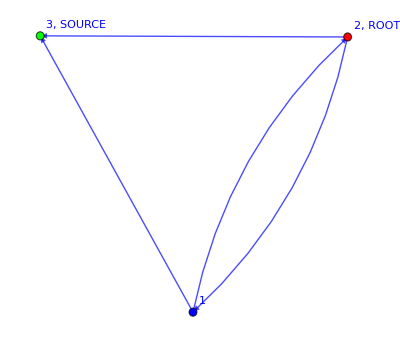

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

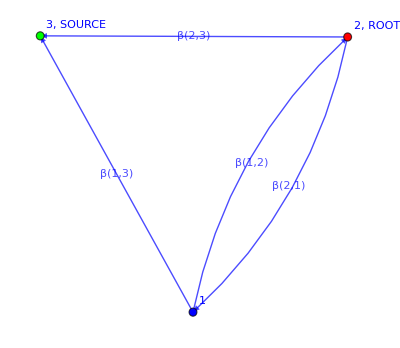

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

## DrawOnGraph[]

“Path” should be made of triplets whose first two elements are the initial and final vertices respectively, while the last is the color of this edge

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

### Usage example of DrawOnGraph[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Graph[EdgeList[myFavoriteGraph],EdgeStyle→{2->1→RGBColor[1, 0, 0],1->3→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},VertexLabels→{PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,ROOT,PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,SOURCE,Name},VertexStyle→{PropertyValue[]⟦1⟧→RGBColor[1, 0, 0],PropertyValue[]⟦1⟧→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

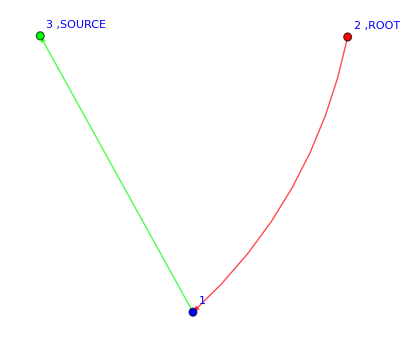

```mathematica
DrawOnGraph[g,path1,"drawOthers"->False]
```

## DrawFromExpression[]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

## AugmentedGraph[]

This is useful to compute the total incoming current from the source towards the DLA cluster/Tree. WE MUST ADD THE EDGE FROM THE OLD SOURCE TO THE NEW SOURCE, AS WELL AS ALLOW THE EDGES FROM THE OLD SOURCE TO THE NEIGHBORS

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

#### Usage example of AugmentedGraph[]

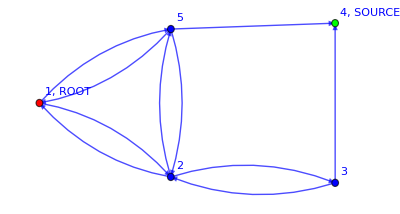

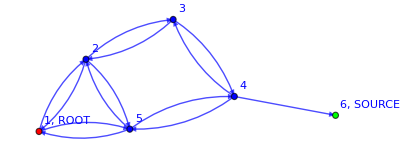
{-Graphics-,4,6}

```mathematica
g=myFavoriteGraph
AugmentedGraph[g]
```

# Field Theory tools

## monoFlatten[]

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

#### Test

## ExtractPaths[]

```mathematica
(*To extract the paths and their weights from the expression of an expectation value*)
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

#### Usage example of ExtractPaths[]

```mathematica
exp=(1-(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 2,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 5,2])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])));ExtractPaths[exp]
```

{{(R_(1,2,RGBColor[1, 0, 0]) β_(1,2) (β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))},{(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))}}

## Laplacian DD[] rules

```mathematica
ClearAll[DD];
(*Remove[DD];*)
DD[0]=0;
DD'[(κ*A_+B_)C_]:=DD[A*C]/(A*C);
DD'[(κ*A_+B_)]:=DD[A]/(A);
(*DD'[a_[x_] b_[y_]]:=1;
DD[a_[x_]*b_[y_]]:=DD[a[x]]*b[y]+DD[b[y]]*a[x]+2∇a[x]*∇b[y];*)
```

#### Tests

```mathematica
DD'[ϕ[x] χ[x]]
```

DD'[ϕ[x] χ[x]]

```mathematica
V[DD[ϕ[x] χ[x]]]/.ϕ[x_]->ϕ[x]+κ δϕ[x]
D[%,κ]
%/.κ->0
```

V[DD[(κ δϕ[x]+ϕ[x]) χ[x]]]

DD[δϕ[x] χ[x]]

DD[δϕ[x] χ[x]]

```mathematica
V[DD[ϕ[x] ]]/.ϕ[x_]->ϕ[x]+κ δϕ[x]
D[%,κ]
%/.κ->0
```

V[DD[κ δϕ[x]+ϕ[x]]]

DD[δϕ[x]]

DD[δϕ[x]]

## Vertex rules

The vertices are where the interaction takes place in the field theory.

```mathematica
ClearAll[V];
V[1.]:=1.;
V[1]:=1;
V[0]:=0;
(*V'[DD[a__]]:=DD[a]/a;(*(ToExpression["δ"<>ToString[a]]);*)*)
V'[a_]:=1;
```

## δrules

```mathematica
ClearAll[Σδrule];
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],

δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>Subscript[n, χ],
δ[a_,a_]/;(MatchQ[a,Subscript[α, __]]):>Subscript[n, α]};
```

```mathematica
ClearAll[δruleExternal]
(*δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, __]]||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, _]])/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[b,Subscript[1, _]])/;(a=!=b):>0 };*)
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

δ[b,b]

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

δ[c,c]

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

ReplaceRepeated::reps: {δruleExternal} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

δ[1,1]//.δruleExternal

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

ReplaceRepeated::reps: {δruleExternal} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

δ[1,2]//.δruleExternal

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

ReplaceRepeated::reps: {δruleExternal} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

δ[1,1] δ[a,a]//.δruleExternal

```mathematica
δ[Subscript[k, 1],Subscript[k, 1]]//.Σδrule
```

δ[k_1,k_1]

```mathematica
δ[Subscript[i, 1],Subscript[i, 1]]//.Σδrule
```

n_χ

```mathematica
δ[Subscript[j, -1],Subscript[j, -1]]//.δruleExternal
```

ReplaceRepeated::reps: {δruleExternal} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

δ[j_-1,j_-1]//.δruleExternal

```mathematica
δ[Subscript[k, -1],Subscript[k, -1]]//.δruleExternal
```

ReplaceRepeated::reps: {δruleExternal} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

δ[k_-1,k_-1]//.δruleExternal

```mathematica
δ[Subscript[1, 1],Subscript[1, -1]]δ[Subscript[1, 1],Subscript[1, -1]]//.Σδrule
```

δ[1_1,1_-1]^2

## FieldsNamesGenerator[]

```mathematica
Clear[FieldsNamesGenerator];
FieldsNamesGenerator[fields_]:=
FieldsNamesGenerator[fields]=Block[{locFields={},starFields={},deltaFields={},deltaStarFields={},l},

locFields=fields;

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

Return[{locFields,starFields,deltaFields,deltaStarFields}]
]
```

#### Test

```mathematica
fields={ϕ,χ};
FieldsNamesGenerator[fields]//AbsoluteTiming
FieldsNamesGenerator[fields]//AbsoluteTiming
```

{0.0007342,{{ϕ,χ},{ϕs,χs},{δϕ,δχ},{δϕs,δχs}}}

{3.7×10^-6,{{ϕ,χ},{ϕs,χs},{δϕ,δχ},{δϕs,δχs}}}

# Vertices contraction

## FreeAction[]

```mathematica
ClearAll[FreeAction];

FreeAction[time_]:=V[1+Sum[Product[ ψs[Subscript[x, ToExpression["action"<>ToString[ time]<>ToString[ index1]]],Subscript[t, time+1]]ψ[Subscript[x, ToExpression["action"<>ToString[ time]<>ToString[ index1]]],Subscript[t, time]],{index1,1,index2}],{index2,1,time}]
];
```

```mathematica
FreeAction[1]
FreeAction[2]
FreeAction[3]
```

V[1+ψ[x_action11,t_1] ψs[x_action11,t_2]]

V[1+ψ[x_action21,t_2] ψs[x_action21,t_3]+2 ψ[x_action21,t_2] ψ[x_action22,t_2] ψs[x_action21,t_3] ψs[x_action22,t_3]]

V[1+ψ[x_action31,t_3] ψs[x_action31,t_4]+2 ψ[x_action31,t_3] ψ[x_action32,t_3] ψs[x_action31,t_4] ψs[x_action32,t_4]+6 ψ[x_action31,t_3] ψ[x_action32,t_3] ψ[x_action33,t_3] ψs[x_action31,t_4] ψs[x_action32,t_4] ψs[x_action33,t_4]]

## SpaceVertices definition

#### WITH POWER COUNTING

```mathematica
ClearAll[Vγ1,Vγ1Minus,Vγ1gχ,Vγ1gχMinus,Vγ1gψ,Vγ1gψMinus,Vγ2,Vγ2Minus,Vγ2gχ,Vγ2gχMinus,Vγ2gψ,Vγ2gψMinus,Vψψ,Vψχ,Vχχ,g];

Vγ1[space_,time_]:= V[γ Subscript[g, γ] ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];

Vγ2[space_,time_]:= V[γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]];
Vγ2Minus[space_,time_]:= V[-γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]]ϕs[space,Subscript[t, time+1]]];

Vψχ[space_,time_]:= V[-g̃ ψ[space,Subscript[t, time]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
(*Vχχ[space_,time_]:= V[-g/2 χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χ[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]];*)
```

#### NO POWER COUNTING

```mathematica
ClearAll[Vγ1,Vγ1Minus,Vγ1gχ,Vγ1gχMinus,Vγ1gψ,Vγ1gψMinus,Vγ2,Vγ2Minus,Vγ2gχ,Vγ2gχMinus,Vγ2gψ,Vγ2gψMinus,Vψψ,Vψχ,Vχχ,g];

Vγ1[space_,time_]:= V[γ1 ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];
Vγ1Minus[space_,time_]:= V[-γ1 ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]];

Vγ1gχ[space_,time_]:= V[γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
Vγ1gχMinus[space_,time_]:= V[-γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];

Vγ1gψ[space_,time_]:= V[γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];
Vγ1gψMinus[space_,time_]:= V[-γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];


Vγ2[space_,time_]:= V[γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψs[space,Subscript[t, time+1]]];
Vγ2Minus[space_,time_]:= V[-γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]]ϕs[space,Subscript[t, time+1]]];

Vγ2gχ[space_,time_]:= V[γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
Vγ2gχMinus[space_,time_]:= V[-γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];

Vγ2gψ[space_,time_]:= V[γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψs[space,Subscript[t, time+1]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];
Vγ2gψMinus[space_,time_]:= V[-γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];

Vψψ[space_,time_]:= V[-g/2 ψ[space,Subscript[t, time]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];
Vψχ[space_,time_]:= V[-g ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
Vχχ[space_,time_]:= V[-g/2 χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χ[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]];
```

## InteractingAction[]

THIS IS ACTUALLY -S

```mathematica
ClearAll[InteractingAction];

InteractingAction[x_,time_]:=Exp[
V[ψs[x,Subscript[t, time+1]]ψ[x,Subscript[t, time]]]+Vγ1[x,time]+Vγ2[x,time]+Vγ2Minus[x,time]+Vψχ[x,time]
];
```

### Test

```mathematica
InteractingAction[x,1]
```

ⅇ^(V[γ2 DD[ϕs[x,t_2] χs[x,1,2,t_1]] ϕ[x,t_1]]+V[-γ2 DD[χs[x,1,2,t_1]] ϕ[x,t_1] ϕs[x,t_2]]+V[-g̃ χ[x,i_1,α_1,t_1] χs[x,i_1,α_1,t_1] ψ[x,t_1]]+V[γ g̃ ϕ[x,t_1] ϕs[x,t_2] χs[x,1,2,t_1] ψs[x,t_2]]+V[ψ[x,t_1] ψs[x,t_2]])

```mathematica
Product[Product[InteractingAction[Subscript[x, j],ii],{ii,0,1}],{j,0,1}]
```

ⅇ^(V[-g̃ χ[x_0,i_1,α_1,t_0] χs[x_0,i_1,α_1,t_0] ψ[x_0,t_0]]+V[-g̃ χ[x_0,i_1,α_1,t_1] χs[x_0,i_1,α_1,t_1] ψ[x_0,t_1]]+V[-g̃ χ[x_1,i_1,α_1,t_0] χs[x_1,i_1,α_1,t_0] ψ[x_1,t_0]]+V[-g̃ χ[x_1,i_1,α_1,t_1] χs[x_1,i_1,α_1,t_1] ψ[x_1,t_1]]+V[γ g̃ ϕ[x_0,t_0] ϕs[x_0,t_1] χs[x_0,1,2,t_0] ψs[x_0,t_1]]+V[γ g̃ ϕ[x_0,t_1] ϕs[x_0,t_2] χs[x_0,1,2,t_1] ψs[x_0,t_2]]+V[γ g̃ ϕ[x_1,t_0] ϕs[x_1,t_1] χs[x_1,1,2,t_0] ψs[x_1,t_1]]+V[γ g̃ ϕ[x_1,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]]+V[ψ[x_0_action0,t_0] ψs[x_0_action0,t_1]]+V[ψ[x_0_action1,t_1] ψs[x_0_action1,t_2]]+V[ψ[x_1_action0,t_0] ψs[x_1_action0,t_1]]+V[ψ[x_1_action1,t_1] ψs[x_1_action1,t_2]])

## WickContractionSpaceVertices[]

```mathematica
ClearAll[WickContractionSpaceVertices];
Options[WickContractionSpaceVertices]={"print"->False,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"#vertices"->10,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True};

WickContractionSpaceVertices[A_ +B_,OptionsPattern[]]:=WickContractionSpaceVertices[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"],"δrule"->OptionValue["δrule"],"δruleExternal"->OptionValue["δruleExternal"],"n_χ"->OptionValue["n_χ"],"n_α"->OptionValue["n_α"],"killψ"->OptionValue["killψ"]]+
WickContractionSpaceVertices[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"],"δrule"->OptionValue["δrule"],"δruleExternal"->OptionValue["δruleExternal"],"n_χ"->OptionValue["n_χ"],"n_α"->OptionValue["n_α"],"killψ"->OptionValue["killψ"]];


WickContractionSpaceVertices[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionSpaceVertices[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex},

z=V[A]*B;

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=1,timeIndex<=(OptionValue["endTime"]),timeIndex++,
z=z*FreeAction[timeIndex];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

If[OptionValue["print"],Print["################## Contracting ",locFields[[l]][x_,Subscript[t, timeIndex]]," ##################"]];

(*
(*Start of loop over the number of vertices*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,
z=z/jj;(*Combinatorial factor*)
*)

(*ZEROTH contribution*)
zTemp1=z//.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*zTemp1=zTemp1//.starFields[[l]][___,Subscript[t, timeIndex]]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
If[OptionValue["print"],Print["First contribution: ",zTemp1]];
];*)
contributions=zTemp1;
If[OptionValue["print"],Print["Zeroth contribution: ",zTemp1]];

(*FIRST contribution*)
zTemp1=z/. locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp1-z=!=0,
zTemp1=D[zTemp1,κ]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];

(*Print["\n",zTemp2];*)

If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,κ]/.κ->0;
];

(*Print[zTemp1,"\n"];*)

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]*δ[{a},{b}]; (*G is the propagator*)

zTemp2=zTemp2//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*DD[deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*C_](*/;(!NumericQ[a*b]):>*):>DD[Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]C]δ[{a},{b}]; (*DD is the laplacian*)

zTemp2=zTemp2//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*DD[deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]](*/;(!NumericQ[a*b]):>*):>DD[Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]]δ[{a},{b}]; (*DD is the laplacian*)

zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;


If[contributions-zTemp1=!=0,
contributions+=zTemp1;
If[OptionValue["print"],Print["First contribution: ",zTemp1]];
];


(*SECOND contribution*)
zTemp1=z/.locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp1-z=!=0,
zTemp1=1/2 D[zTemp1,{κ,2}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,2}]/.κ->0;
];

zTemp1=Expand[zTemp1];

zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][z_,c___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]Subscript[G, locFields[[l]]][x,z,Subscript[t, timeIndex]]*δ[{a},{b}]δ[{a},{c}]; (*G is the propagator*)
(*The one with the laplacian should not be there*)

zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
If[OptionValue["print"],Print["Second contribution: ",zTemp1]];
];

(*THIRD contribution*)
zTemp1=z/.locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp1-z=!=0,
zTemp1=1/(2*3)D[zTemp1,{κ,3}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,3}]/.κ->0;
];

zTemp1=Expand[zTemp1];

zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][z_,c___,Subscript[t, timeIndex]]*deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][q_,d___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]Subscript[G, locFields[[l]]][x,z,Subscript[t, timeIndex]]Subscript[G, locFields[[l]]][x,q,Subscript[t, timeIndex]]*δ[{a},{b}]δ[{a},{c}]δ[{a},{d}]; (*G is the propagator*)
(*The one with the laplacian should not be there*)

zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
If[OptionValue["print"],Print["Third contribution: ",zTemp1]];
];

z=contributions;


If[OptionValue["print"],
Print["Overall contributions: ",contributions];
Print["################################################################################################"]];

contributions=0;

(*];(*End of loop over number of vertices*)*)

z=z/.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*z=z/.starFields[[l]][___,Subscript[t, timeIndex]]->0;*)

z=z//.δ[{a_,c___},{b_,d___}]:>δ[a,b]δ[{c},{d}]//.δ[{},{}]:>1;

If[OptionValue["δrule"],z=z//.Σδrule];
If[OptionValue["δruleExternal"],z=z//.δ[a_,b_]starFields[[l]][c___,a_,d___,Subscript[t, timeIndex]]/;(NumericQ[b] && !NumericQ[a]):>δ[a,b]starFields[[l]][c,b,d,Subscript[t, timeIndex]]/.δ[a_,b_]/;(NumericQ[b] && !NumericQ[a]):>1;
z=z//.δ[a_,b_]starFields[[l]][c___,b_,d___,Subscript[t, timeIndex]]/;(NumericQ[a] && !NumericQ[b]):>δ[a,b]starFields[[l]][c,a,d,Subscript[t, timeIndex]]/.δ[a_,b_]/;(NumericQ[a] && !NumericQ[b]):>1
];

];(*End of loop over fields*)

z=z/.Subscript[n, χ]->OptionValue["n_χ"];
z=z/.Subscript[n, α]->OptionValue["n_α"];
z=z/.Subscript[G, ψ][Subscript[x, action],Subscript[x, action],__]->0;

];(*End of loop over time*)

If[OptionValue["killψ"],z=z/.ψs[___,Subscript[t, a_]]/;(a<OptionValue["endTime"]+1):>0];

Return[z]
];
```

#### Test

```mathematica
WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]ϕs[Subscript[x, 2],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

γ1 ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_2,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0)]
```

γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_3] ψs[x_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_action2,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1gχ[Subscript[x, 1],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->2]
```

γ1g ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_action1,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1] G_ψ[x_action1,x_1,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]ψs[Subscript[x, 3],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vψχ[Subscript[x, 2],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 ϕs[x_1,t_2] χs[x_2,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_2,x_3,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_2,t_3] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_3,x_2,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ2[Subscript[x, 1],1]ϕ[Subscript[x, 2],Subscript[t, 2]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

γ2 DD[χs[x_1,1,2,t_1] G_ϕ[x_2,x_1,t_2]] ψs[x_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_action2,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ2[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 γ2 DD[ϕs[x_2,t_3] G_χ[x_3,x_2,t_2]] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_2,t_3] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

## WickContractionSpaceVerticesMOD[]

### CombinatorialFactor[]

```mathematica
ClearAll[CombinatorialFactor];

CombinatorialFactor[A_+B___,max_,time_]:=CombinatorialFactor[A,max,time]+CombinatorialFactor[(Plus@@{B}),max,time];

CombinatorialFactor[expr_,max_,time_]:=Module[{factors,chis,others,n},
If[Head[expr]===Times,
(* TRUE *)
factors=List@@expr;
chis=Select[factors,!FreeQ[#,g̃]&&!FreeQ[#,Subscript[t, time]]&];
others=Complement[factors,chis];(*conservatively:remove χs only*)
n=Length[chis];
If[n>0&&n<=max,
Return[Factorial[n]*Times@@chis*Times@@others],
Return[expr]],

(* ELSE *)
Return[expr]
]; (* END OF FIRST IF*)
];(* END OF MODULE*)
```

```mathematica
expr=s+Vψχ[Subscript[x, 1],2]Vγ1[Subscript[x, 1],2]+Vψχ[Subscript[x, 1],2]Vψχ[Subscript[x, 12],2]+Vψχ[Subscript[x, 1],2]Vψχ[Subscript[x, 12],2]Vψχ[Subscript[x, 13],2];

expr=CombinatorialFactor[expr,4,2]
```

s+2 V[-g̃ χ[x_1,i_1,α_1,t_2] χs[x_1,i_1,α_1,t_2] ψ[x_1,t_2]] V[-g̃ χ[x_12,i_1,α_1,t_2] χs[x_12,i_1,α_1,t_2] ψ[x_12,t_2]]+6 V[-g̃ χ[x_1,i_1,α_1,t_2] χs[x_1,i_1,α_1,t_2] ψ[x_1,t_2]] V[-g̃ χ[x_12,i_1,α_1,t_2] χs[x_12,i_1,α_1,t_2] ψ[x_12,t_2]] V[-g̃ χ[x_13,i_1,α_1,t_2] χs[x_13,i_1,α_1,t_2] ψ[x_13,t_2]]+V[-g̃ χ[x_1,i_1,α_1,t_2] χs[x_1,i_1,α_1,t_2] ψ[x_1,t_2]] V[γ g_γ ϕ[x_1,t_2] ϕs[x_1,t_3] χs[x_1,1,2,t_2] ψs[x_1,t_3]]

### WickContractionSpaceVerticesMOD[]

```mathematica
ClearAll[WickContractionSpaceVerticesMOD];
Options[WickContractionSpaceVerticesMOD]={"print"->False,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"#vertices"->10,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"maxContractions"->5,"killψ"->True};

WickContractionSpaceVerticesMOD[A_ +B_,OptionsPattern[]]:=WickContractionSpaceVerticesMOD[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"],"δrule"->OptionValue["δrule"],"δruleExternal"->OptionValue["δruleExternal"],"n_χ"->OptionValue["n_χ"],"n_α"->OptionValue["n_α"],"maxContractions"->OptionValue["maxContractions"],"killψ"->OptionValue["killψ"]]+
WickContractionSpaceVerticesMOD[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"],"δrule"->OptionValue["δrule"],"δruleExternal"->OptionValue["δruleExternal"],"n_χ"->OptionValue["n_χ"],"n_α"->OptionValue["n_α"],"maxContractions"->OptionValue["maxContractions"],"killψ"->OptionValue["killψ"]];


WickContractionSpaceVerticesMOD[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionSpaceVerticesMOD[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex,ii,ss},

z=V[A]*B;

(* NEW BIT *)
If[!FreeQ[z,g̃],
(* TRUE *)


If[OptionValue["print"],Print["TRUE: z before =", z]];
z=z//.Vψχ[Subscript[x, a_],t]:>(Sum[Vψχ[Subscript[x, a],timeIndex],{timeIndex,(a-100),OptionValue["endTime"]}])//Expand;(* a must be given as 100+(Natural Numbers)*)
If[OptionValue["print"],Print["\n z after =",z]];
];

(* NEW BIT *)
For[timeIndex=1,timeIndex<=(OptionValue["endTime"]),timeIndex++,

z=CombinatorialFactor[z,OptionValue["endTime"],timeIndex];
];


locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=1,timeIndex<=(OptionValue["endTime"]),timeIndex++,

z=z*FreeAction[timeIndex];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

If[OptionValue["print"],Print["################## Contracting ",locFields[[l]][x_,Subscript[t, timeIndex]]," ##################"]];

(*
(*Start of loop over the number of vertices*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,
z=z/jj;(*Combinatorial factor*)
*)

(*ZEROTH contribution*)

zTemp1=z//.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*(* TEST WITH REPLACE *)
zTemp1=Replace[z,{locFields[[l]][___,Subscript[t, timeIndex]]->0},{1,4}];*)


(*zTemp1=zTemp1//.starFields[[l]][___,Subscript[t, timeIndex]]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
If[OptionValue["print"],Print["First contribution: ",zTemp1]];
];*)

contributions=zTemp1;
If[OptionValue["print"],Print["Zeroth contribution: ",contributions]];


(* NEW BIT *)

zTemp1=z;

ii=0;

While[!FreeQ[zTemp1,starFields[[l]][___,Subscript[t, timeIndex]]]&& ii<OptionValue["maxContractions"],

ii++;
(* EXTRA MODIFICATION: instead of derivating n times and the contract, I think it is better to derivate once, contract, and the iterate n times. This is what I implement now*)
For[ss=1,ss<=ii,ss++,
zTemp2=zTemp1/. locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
(*zTemp1=Replace[z,{ locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]]},{1,4}];*)

If[zTemp1-zTemp2=!=0,
(*zTemp1=1/Factorial[ii] D[zTemp1,{κ,ii}]/.κ->0;*)
zTemp1=1/ss D[zTemp2,{κ}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];
(*zTemp2=Replace[zTemp1,{ starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]]},{1,4}];*)

(*Print["\n",zTemp2];*)

If[zTemp2-zTemp1=!=0,
(*zTemp1=1/Factorial[ii] D[zTemp2,{κ,ii}]/.κ->0;*)
zTemp1=1/ss D[zTemp2,{κ}]/.κ->0;
];

(*Print[zTemp1,"\n"];*)

(* CONTRACTION *)
zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]*δ[{a},{b}]; (*G is the propagator*)
(*zTemp2=Replace[zTemp1,{ deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]*δ[{a},{b}]},{1,2}];*)

(* LAPLACIAN
zTemp2=zTemp2//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*DD[deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*C_](*/;(!NumericQ[a*b]):>*):>DD[Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]C]δ[{a},{b}]; (*DD is the laplacian*)

zTemp2=zTemp2//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*DD[deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]](*/;(!NumericQ[a*b]):>*):>DD[Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]]δ[{a},{b}]; (*DD is the laplacian*)
*)
zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;

];(* END OF "FOR" ON DERIVATIONS+CONTRACTIONS*)

zTemp1=zTemp1/.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*z=z/.starFields[[l]][___,Subscript[t, timeIndex]]->0;*)

If[contributions-zTemp1=!=0 && zTemp1=!=0 ,
contributions+=zTemp1;
If[OptionValue["print"],Print["Contribution #",ii,": ",zTemp1]];
];

zTemp1=z;

];(* END OF WHILE*)

z=contributions;

If[OptionValue["print"],
Print["Overall contributions: ",contributions];
Print["################################################################################################"]];

contributions=0;

(*];(*End of loop over number of vertices*)*)

z=z/.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*z=z/.starFields[[l]][___,Subscript[t, timeIndex]]->0;*)

z=z//.δ[{a_,c___},{b_,d___}]:>δ[a,b]δ[{c},{d}]//.δ[{},{}]:>1;

If[OptionValue["δrule"],z=z//.Σδrule];
If[OptionValue["δruleExternal"],z=z//.δ[a_,b_]starFields[[l]][c___,a_,d___,Subscript[t, timeIndex]]/;(NumericQ[b] && !NumericQ[a]):>δ[a,b]starFields[[l]][c,b,d,Subscript[t, timeIndex]]/.δ[a_,b_]/;(NumericQ[b] && !NumericQ[a]):>1;
z=z//.δ[a_,b_]starFields[[l]][c___,b_,d___,Subscript[t, timeIndex]]/;(NumericQ[a] && !NumericQ[b]):>δ[a,b]starFields[[l]][c,a,d,Subscript[t, timeIndex]]/.δ[a_,b_]/;(NumericQ[a] && !NumericQ[b]):>1
];

z=z/.Subscript[n, χ]->OptionValue["n_χ"];
z=z/.Subscript[n, α]->OptionValue["n_α"];

];(*End of loop over fields*)

z=z/.Subscript[G, ψ][Subscript[x, action],Subscript[x, action],__]->0/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0;

];(*End of loop over time*)

If[OptionValue["killψ"],
z=z/.ψs[___,Subscript[t, a_]]/;(a<=OptionValue["endTime"]):>0
];

Clear[locFields, starFields, deltaFields,deltaStarFields,contributions,zTemp1,zTemp2,κ,jj,l,timeIndex,ii,ss];
Return[z]
];
```

### I don’t remember what this is

```mathematica
WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]ϕs[Subscript[x, 2],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

γ1 ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_2,t_1]

```mathematica
WickContractionSpaceVerticesMOD[Vγ1[Subscript[x, 1],1]ϕs[Subscript[x, 2],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"maxContractions"->5]
```

γ1 ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_2,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0)]
```

γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_3] ψs[x_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_action2,x_1,t_2]

```mathematica
WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"maxContractions"->5]
```

γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_3] ψs[x_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_action2,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]ψs[Subscript[x, 3],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vψχ[Subscript[x, 2],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 ϕs[x_1,t_2] χs[x_2,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_2,x_3,t_1]

```mathematica
WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]ψs[Subscript[x, 3],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vψχ[Subscript[x, 2],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 ϕs[x_1,t_2] χs[x_2,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_2,x_3,t_1]

```mathematica
(* With the previously checked examples it works. Let's see if it does what I need*)
```

Multiple fields:

```mathematica
WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vγ1[Subscript[x, 3],3]Vψχ[Subscript[x, 4],2]Vψχ[Subscript[x, 5],3] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]
```

0

```mathematica
WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vγ1[Subscript[x, 3],3]Vψχ[Subscript[x, 4],2]Vψχ[Subscript[x, 5],3] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->False]
```

g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_4,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_3,t_4] ψs[x_4,t_3] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_2,t_2] G_χ[x_5,x_3,t_3] G_ψ[x_4,x_1,t_2] G_ψ[x_5,x_2,t_3]+g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_4,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_2,t_3] ψs[x_3,t_4] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_2,t_2] G_χ[x_5,x_3,t_3] G_ψ[x_4,x_1,t_2] G_ψ[x_5,x_4,t_3]

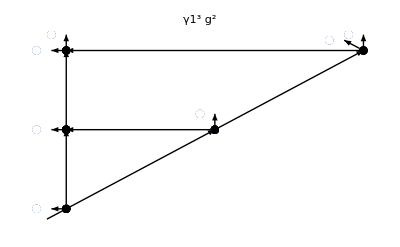

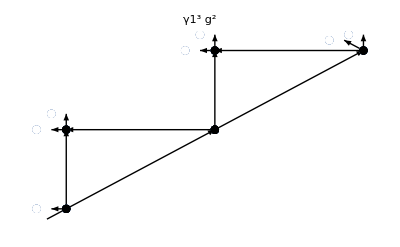

```mathematica
DrawFromContraction[%]
```

```mathematica
WickContractionSpaceVerticesMOD[Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vγ1[Subscript[x, 3],3]Vψχ[Subscript[x, 4],2]Vψχ[Subscript[x, 5],3] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_4,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_3,t_4] ψs[x_5,t_4] ψs[x_action3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_2,t_2] G_χ[x_5,x_3,t_3] G_ψ[x_4,x_1,t_2] G_ψ[x_5,x_2,t_3] G_ψ[x_action3,x_4,t_3]

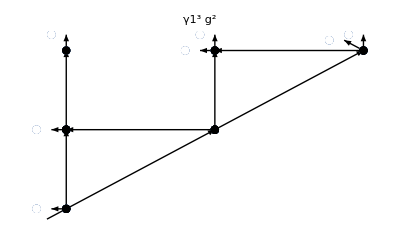

```mathematica
DrawFromContraction[%]
```

```mathematica
(* SEEMS TO BE WORKING *)
```

### Test with InteractingAction[]

Using vertices explicitly

```mathematica
WickContractionSpaceVerticesMOD[Vγ1[Subscript[x, 1],1]ϕs[Subscript[x, 2],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_2,t_1]

Using the partition function

Single time slice

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, j],ii],{ii,1,1}],{j,1,2}]
```

ⅇ^(V[-g̃ χ[x_1,i_1,α_1,t_1] χs[x_1,i_1,α_1,t_1] ψ[x_1,t_1]]+V[-g̃ χ[x_2,i_1,α_1,t_1] χs[x_2,i_1,α_1,t_1] ψ[x_2,t_1]]+V[γ g̃ ϕ[x_1,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]]+V[γ g̃ ϕ[x_2,t_1] ϕs[x_2,t_2] χs[x_2,1,2,t_1] ψs[x_2,t_2]]+V[ψ[x_1_action1,t_1] ψs[x_1_action1,t_2]]+V[ψ[x_2_action1,t_1] ψs[x_2_action1,t_2]])

```mathematica
WickContractionSpaceVerticesMOD[V[ϕs[Subscript[x, 2],Subscript[t, 1]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]
```

V[ϕs[x_2,t_1]]+γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_2,t_1]+γ g̃ ϕs[x_2,t_2] χs[x_2,1,2,t_1] ψs[x_2,t_2] G_ϕ[x_2,x_2,t_1]

Two time slices

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, spaceIndex],timeIndex],{timeIndex,1,2}],{spaceIndex,0,1}];
```

```mathematica
OneLoop=WickContractionSpaceVerticesMOD[V[ϕs[Subscript[x, 0],Subscript[t, 1]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0
```

V[ϕs[x_0,t_1]]-γ^2 (g̃)^3 ϕs[x_0,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_2]+γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_0_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_0_action2,x_1,t_2]+γ^2 (g̃)^2 ϕs[x_0,t_3] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3] ψs[x_0_action2,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_0_action2,x_1,t_2]+γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_1_action2,x_1,t_2]+γ^2 (g̃)^2 ϕs[x_0,t_3] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3] ψs[x_1_action2,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1_action2,x_1,t_2]

```mathematica
OneLoop=OneLoop/.V[_]->0/.ψs[Subscript[Subscript[x, _], action2],_]->0 
OneLoopList=List @@ (%)/.Sum->List
```

-γ^2 (g̃)^3 ϕs[x_0,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_2]

{-1,γ^2,(g̃)^3,ϕs[x_0,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_0,t_3],G_ϕ[x_0,x_1,t_2],G_ϕ[x_1,x_0,t_1],G_χ[x_1,x_0,t_2],G_ψ[x_1,x_1,t_2]}

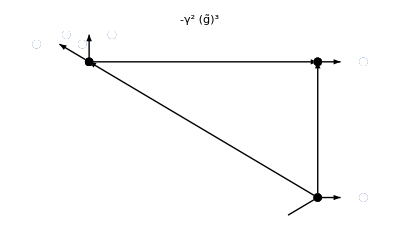

-Graphics-

2 Null

```mathematica
DrawFromContraction[OneLoop[[2]]+OneLoop[[3]]]
```

Are Multiple g contractions allowed? YES THEY ARE

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, spaceIndex],timeIndex],{timeIndex,1,2}],{spaceIndex,0,2}]
```

ⅇ^(V[-g̃ χ[x_0,i_1,α_1,t_1] χs[x_0,i_1,α_1,t_1] ψ[x_0,t_1]]+V[-g̃ χ[x_0,i_1,α_1,t_2] χs[x_0,i_1,α_1,t_2] ψ[x_0,t_2]]+V[-g̃ χ[x_1,i_1,α_1,t_1] χs[x_1,i_1,α_1,t_1] ψ[x_1,t_1]]+V[-g̃ χ[x_1,i_1,α_1,t_2] χs[x_1,i_1,α_1,t_2] ψ[x_1,t_2]]+V[-g̃ χ[x_2,i_1,α_1,t_1] χs[x_2,i_1,α_1,t_1] ψ[x_2,t_1]]+V[-g̃ χ[x_2,i_1,α_1,t_2] χs[x_2,i_1,α_1,t_2] ψ[x_2,t_2]]+V[γ g̃ ϕ[x_0,t_1] ϕs[x_0,t_2] χs[x_0,1,2,t_1] ψs[x_0,t_2]]+V[γ g̃ ϕ[x_0,t_2] ϕs[x_0,t_3] χs[x_0,1,2,t_2] ψs[x_0,t_3]]+V[γ g̃ ϕ[x_1,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]]+V[γ g̃ ϕ[x_1,t_2] ϕs[x_1,t_3] χs[x_1,1,2,t_2] ψs[x_1,t_3]]+V[γ g̃ ϕ[x_2,t_1] ϕs[x_2,t_2] χs[x_2,1,2,t_1] ψs[x_2,t_2]]+V[γ g̃ ϕ[x_2,t_2] ϕs[x_2,t_3] χs[x_2,1,2,t_2] ψs[x_2,t_3]])

```mathematica
WickContractionSpaceVerticesMOD[V[χs[Subscript[x, 0],1,2,Subscript[t, 1]]ψs[Subscript[x, 1],Subscript[t, 1]]ψs[Subscript[x, 2],Subscript[t, 1]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0
```

(g̃)^2 χs[x_2,1,2,t_1] G_χ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_1]

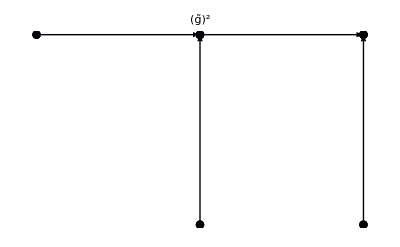

```mathematica
DrawFromContraction[%]
```

```mathematica
(* YES THEY ARE*)
```

Are they also allowed with psi’s coming from different pasts?

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, spaceIndex],timeIndex],{timeIndex,0,2}],{spaceIndex,0,2}]
```

ⅇ^(V[-g̃ χ[x_0,i_1,α_1,t_0] χs[x_0,i_1,α_1,t_0] ψ[x_0,t_0]]+V[-g̃ χ[x_0,i_1,α_1,t_1] χs[x_0,i_1,α_1,t_1] ψ[x_0,t_1]]+V[-g̃ χ[x_0,i_1,α_1,t_2] χs[x_0,i_1,α_1,t_2] ψ[x_0,t_2]]+V[-g̃ χ[x_1,i_1,α_1,t_0] χs[x_1,i_1,α_1,t_0] ψ[x_1,t_0]]+V[-g̃ χ[x_1,i_1,α_1,t_1] χs[x_1,i_1,α_1,t_1] ψ[x_1,t_1]]+V[-g̃ χ[x_1,i_1,α_1,t_2] χs[x_1,i_1,α_1,t_2] ψ[x_1,t_2]]+V[-g̃ χ[x_2,i_1,α_1,t_0] χs[x_2,i_1,α_1,t_0] ψ[x_2,t_0]]+V[-g̃ χ[x_2,i_1,α_1,t_1] χs[x_2,i_1,α_1,t_1] ψ[x_2,t_1]]+V[-g̃ χ[x_2,i_1,α_1,t_2] χs[x_2,i_1,α_1,t_2] ψ[x_2,t_2]]+V[γ g̃ ϕ[x_0,t_0] ϕs[x_0,t_1] χs[x_0,1,2,t_0] ψs[x_0,t_1]]+V[ψ[x_0,t_0] ψs[x_0,t_1]]+V[γ g̃ ϕ[x_0,t_1] ϕs[x_0,t_2] χs[x_0,1,2,t_1] ψs[x_0,t_2]]+V[ψ[x_0,t_1] ψs[x_0,t_2]]+V[γ g̃ ϕ[x_0,t_2] ϕs[x_0,t_3] χs[x_0,1,2,t_2] ψs[x_0,t_3]]+V[ψ[x_0,t_2] ψs[x_0,t_3]]+V[γ g̃ ϕ[x_1,t_0] ϕs[x_1,t_1] χs[x_1,1,2,t_0] ψs[x_1,t_1]]+V[ψ[x_1,t_0] ψs[x_1,t_1]]+V[γ g̃ ϕ[x_1,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]]+V[ψ[x_1,t_1] ψs[x_1,t_2]]+V[γ g̃ ϕ[x_1,t_2] ϕs[x_1,t_3] χs[x_1,1,2,t_2] ψs[x_1,t_3]]+V[ψ[x_1,t_2] ψs[x_1,t_3]]+V[γ g̃ ϕ[x_2,t_0] ϕs[x_2,t_1] χs[x_2,1,2,t_0] ψs[x_2,t_1]]+V[ψ[x_2,t_0] ψs[x_2,t_1]]+V[γ g̃ ϕ[x_2,t_1] ϕs[x_2,t_2] χs[x_2,1,2,t_1] ψs[x_2,t_2]]+V[ψ[x_2,t_1] ψs[x_2,t_2]]+V[γ g̃ ϕ[x_2,t_2] ϕs[x_2,t_3] χs[x_2,1,2,t_2] ψs[x_2,t_3]]+V[ψ[x_2,t_2] ψs[x_2,t_3]])

```mathematica
WickContractionSpaceVerticesMOD[V[χs[Subscript[x, 0],1,2,Subscript[t, 1]]ψs[Subscript[x, 1],Subscript[t, 1]]ψs[Subscript[x, 2],Subscript[t, 0]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0
```

χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_2] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_2] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_2] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_0,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_1,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_1,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_1,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_1,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_1,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_0,t_2]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_0,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_2,t_2] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_0,t_2] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_2] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_0,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_0,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_0,x_2,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_2] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_1,t_2] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]+(g̃)^2 χs[x_2,1,2,t_1] G_χ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_2] G_ψ[x_0,x_1,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_0,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_1,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_0,x_2,t_2] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_0,x_2,t_2] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_2] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_2] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_1,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_1,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_1,t_3] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_1,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_2,t_2] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_0,t_2] G_ψ[x_2,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_2,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_0,t_2] G_ψ[x_2,x_1,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_1,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_1,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_1,t_2]+χs[x_0,1,2,t_1] ψs[x_2,t_2] ψs[x_2,t_3] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_1,t_2]-g̃ χs[x_2,1,2,t_1] ψs[x_2,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_1,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_2] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_2] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_0,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_0,x_1,t_2] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_1,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_0,t_2] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]-g̃ χs[x_1,1,2,t_1] ψs[x_1,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_0,t_2] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_0,t_2] G_ψ[x_2,x_2,t_0]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_0,t_2] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_2,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_1,t_2] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_3] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_1,t_2] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_0,t_2] G_ψ[x_1,x_2,t_1] G_ψ[x_2,x_1,t_2] G_ψ[x_2,x_2,t_0]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_2,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_0,t_2] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_2] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_0,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_0,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_0,x_2,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_0,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_1,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_0,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_2] G_χ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_1,t_2] G_χ[x_2,x_0,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+(g̃)^2 χs[x_2,1,2,t_1] G_χ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_2] G_ψ[x_0,x_1,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_0,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_1,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_2] G_ψ[x_0,x_2,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_2,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_1,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_1,t_3] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_1,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_2,t_2] ψs[x_2,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_0,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_2,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_0,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_2,t_2] ψs[x_2,t_3] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_1,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_2,t_3] G_χ[x_2,x_0,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_1,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_3] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_2] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_3] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_1,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_2,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_3] G_ψ[x_0,x_0,t_2] G_ψ[x_0,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_3] G_ψ[x_0,x_1,t_1] G_ψ[x_1,x_0,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_3] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_3] G_χ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_0,t_3] ψs[x_2,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]+χs[x_0,1,2,t_1] ψs[x_1,t_3] ψs[x_2,t_3] G_ψ[x_1,x_1,t_1] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_0] G_ψ[x_2,x_2,t_1] G_ψ[x_2,x_2,t_2]

ReplaceRepeated::rrlim: Exiting after χs[x_0,1,2,t_1] ψs[x_0,t_2] ψs[x_1,t_2] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]-g̃ χs[x_1,1,2,t_1] ψs[x_0,t_2] G_χ[x_1,x_0,t_1] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1]+«9»+χs[x_0,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_3] G_ψ[x_0,x_0,t_1] G_ψ[x_0,x_2,t_0] G_ψ[x_1,x_1,t_1] G_ψ[x_2,x_0,t_2]+«84» scanned 65536 times.

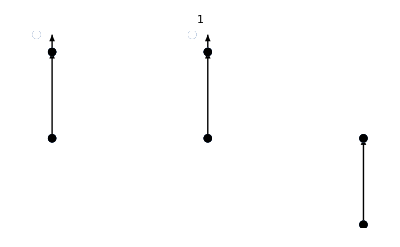

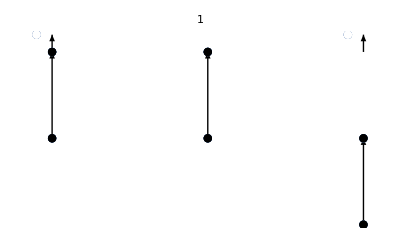

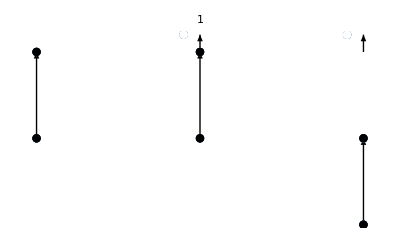

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

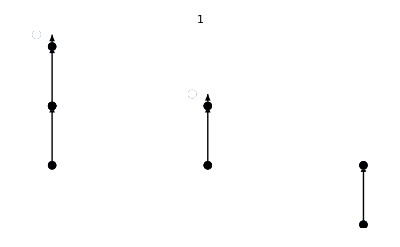

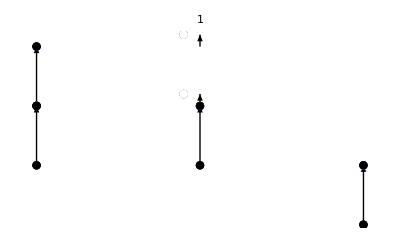

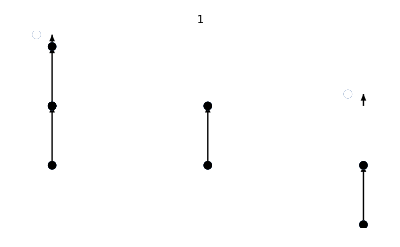

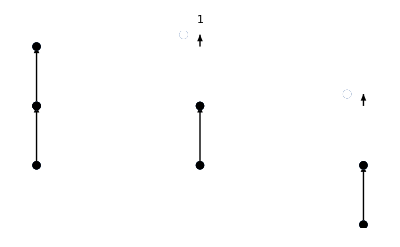

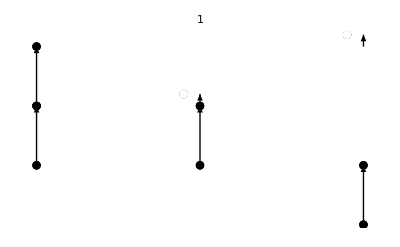

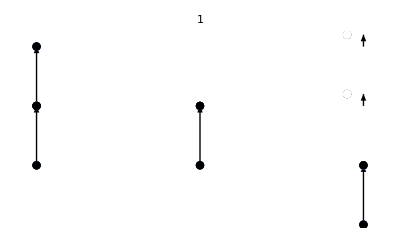

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

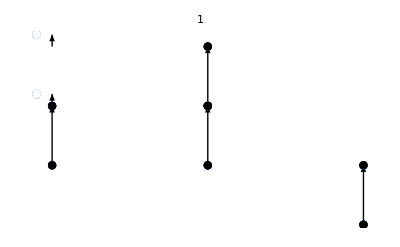

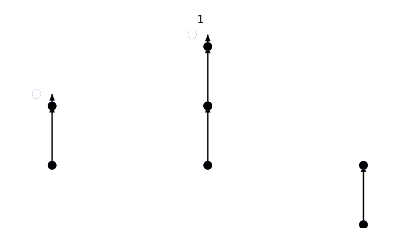

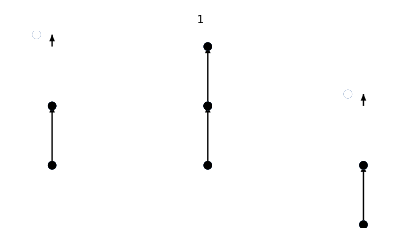

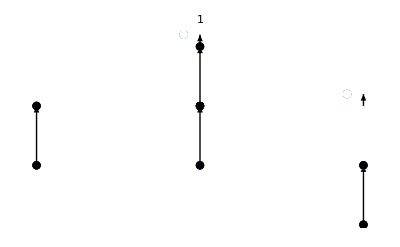

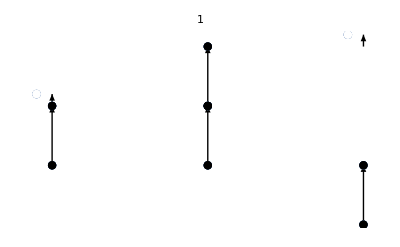

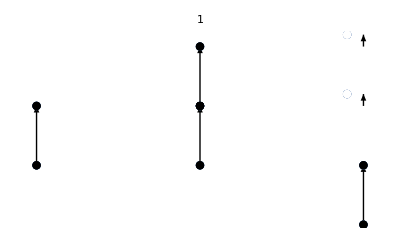

-Graphics-

-Graphics-

-Graphics-

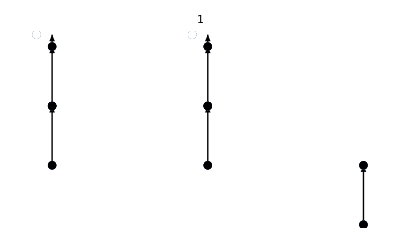

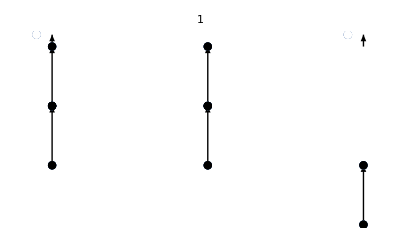

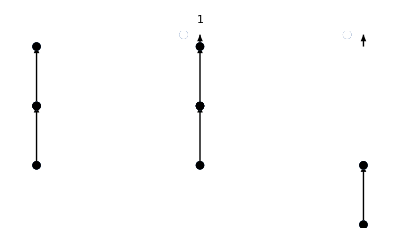

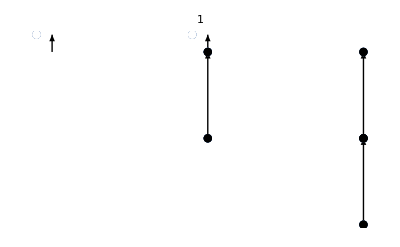

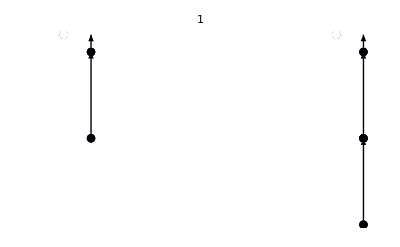

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

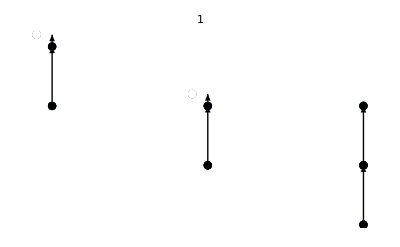

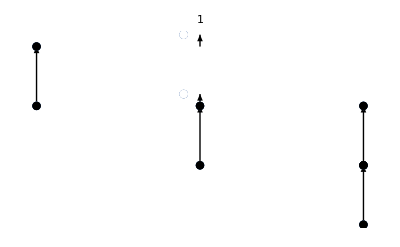

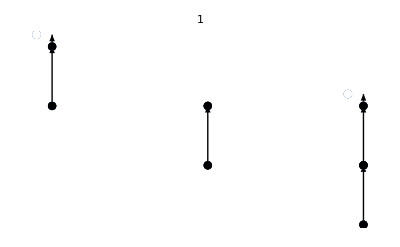

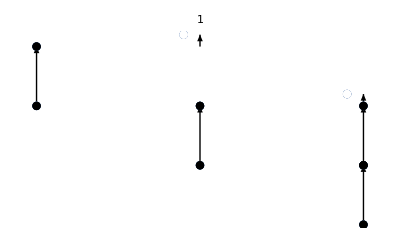

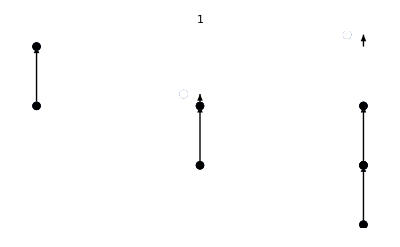

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

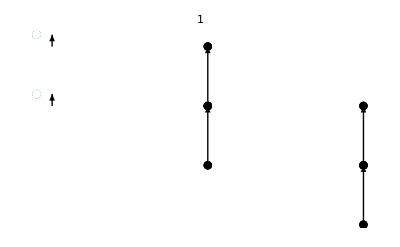

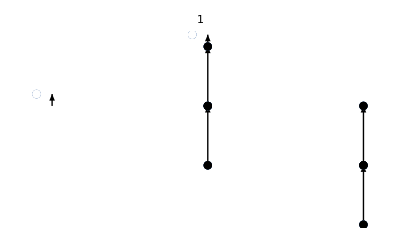

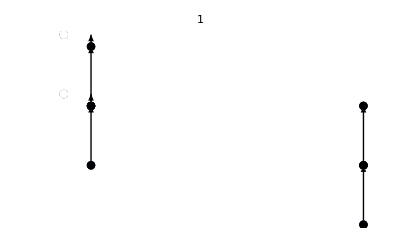

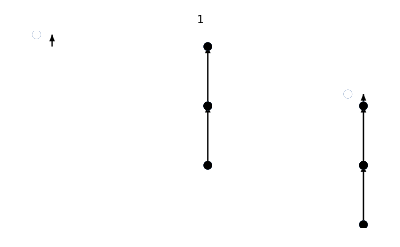

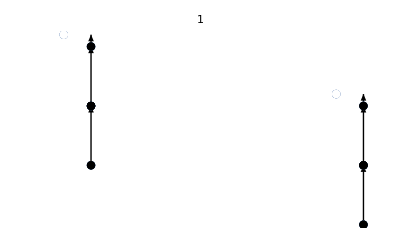

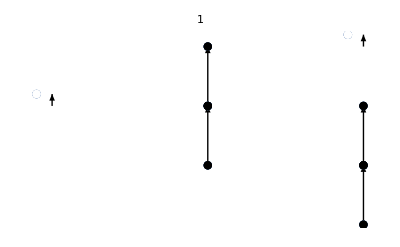

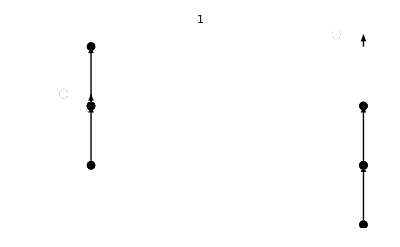

-Graphics-

-Graphics-

-Graphics-

-Graphics-

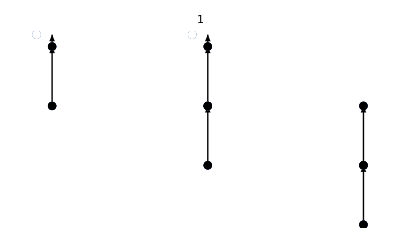

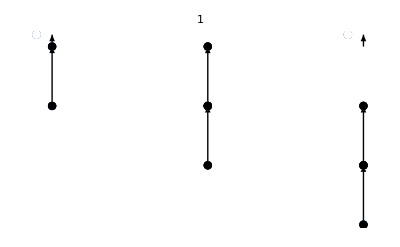

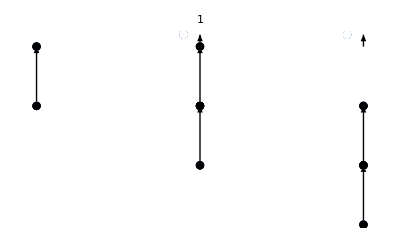

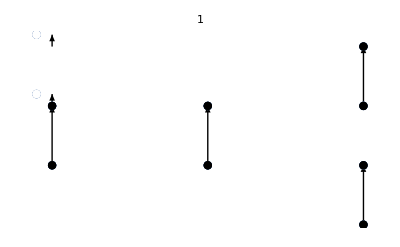

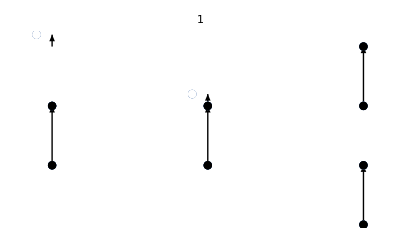

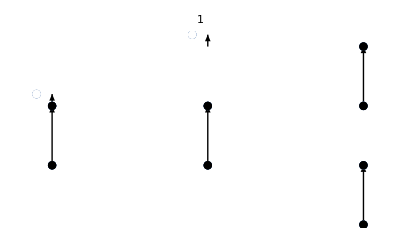

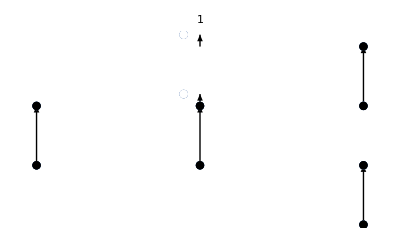

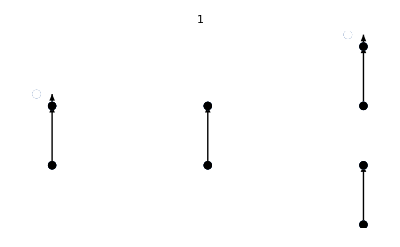

-Graphics-

-Graphics-

-Graphics-

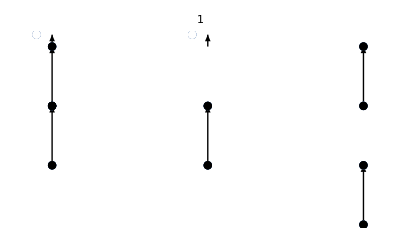

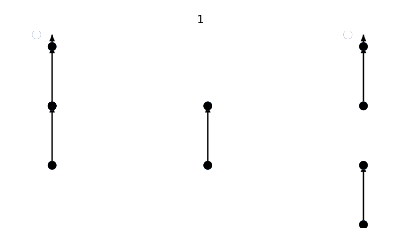

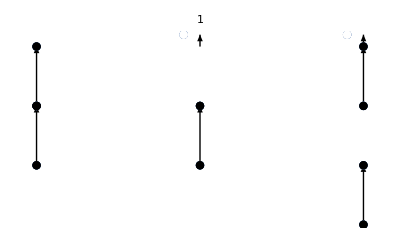

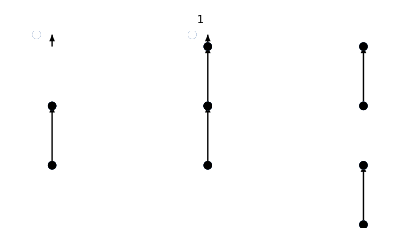

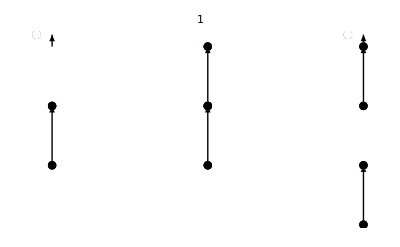

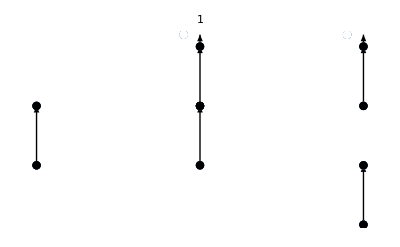

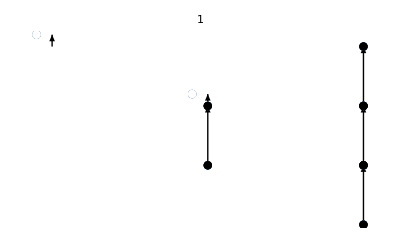

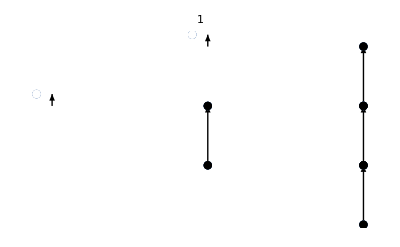

-Graphics-

-Graphics-

-Graphics-

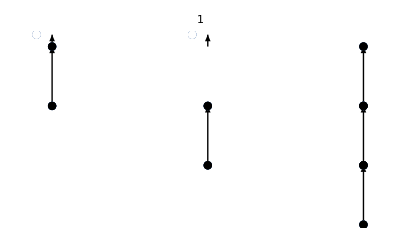

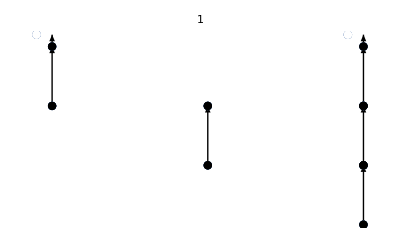

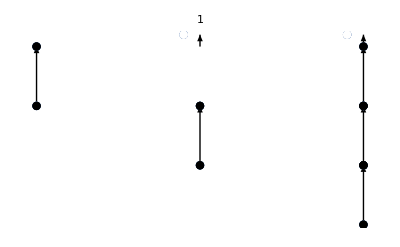

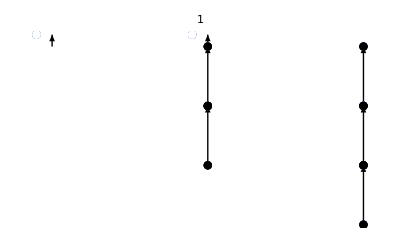

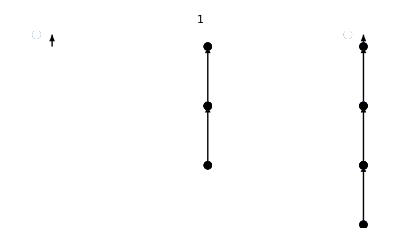

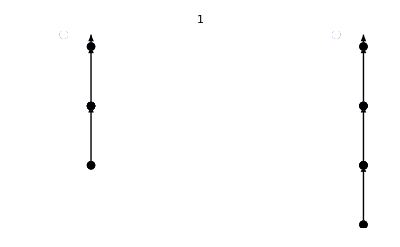

```mathematica
DrawFromContraction[%]
```

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, spaceIndex],timeIndex],{timeIndex,0,2}],{spaceIndex,0,2}]/.ψ[a_,_] ψs[a_,_]->0
```

ⅇ^(V[-g̃ χ[x_0,i_1,α_1,t_0] χs[x_0,i_1,α_1,t_0] ψ[x_0,t_0]]+V[-g̃ χ[x_0,i_1,α_1,t_1] χs[x_0,i_1,α_1,t_1] ψ[x_0,t_1]]+V[-g̃ χ[x_0,i_1,α_1,t_2] χs[x_0,i_1,α_1,t_2] ψ[x_0,t_2]]+V[-g̃ χ[x_1,i_1,α_1,t_0] χs[x_1,i_1,α_1,t_0] ψ[x_1,t_0]]+V[-g̃ χ[x_1,i_1,α_1,t_1] χs[x_1,i_1,α_1,t_1] ψ[x_1,t_1]]+V[-g̃ χ[x_1,i_1,α_1,t_2] χs[x_1,i_1,α_1,t_2] ψ[x_1,t_2]]+V[-g̃ χ[x_2,i_1,α_1,t_0] χs[x_2,i_1,α_1,t_0] ψ[x_2,t_0]]+V[-g̃ χ[x_2,i_1,α_1,t_1] χs[x_2,i_1,α_1,t_1] ψ[x_2,t_1]]+V[-g̃ χ[x_2,i_1,α_1,t_2] χs[x_2,i_1,α_1,t_2] ψ[x_2,t_2]]+V[γ g̃ ϕ[x_0,t_0] ϕs[x_0,t_1] χs[x_0,1,2,t_0] ψs[x_0,t_1]]+V[γ g̃ ϕ[x_0,t_1] ϕs[x_0,t_2] χs[x_0,1,2,t_1] ψs[x_0,t_2]]+V[γ g̃ ϕ[x_0,t_2] ϕs[x_0,t_3] χs[x_0,1,2,t_2] ψs[x_0,t_3]]+V[γ g̃ ϕ[x_1,t_0] ϕs[x_1,t_1] χs[x_1,1,2,t_0] ψs[x_1,t_1]]+V[γ g̃ ϕ[x_1,t_1] ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2]]+V[γ g̃ ϕ[x_1,t_2] ϕs[x_1,t_3] χs[x_1,1,2,t_2] ψs[x_1,t_3]]+V[γ g̃ ϕ[x_2,t_0] ϕs[x_2,t_1] χs[x_2,1,2,t_0] ψs[x_2,t_1]]+V[γ g̃ ϕ[x_2,t_1] ϕs[x_2,t_2] χs[x_2,1,2,t_1] ψs[x_2,t_2]]+V[γ g̃ ϕ[x_2,t_2] ϕs[x_2,t_3] χs[x_2,1,2,t_2] ψs[x_2,t_3]])

```mathematica
WickContractionSpaceVerticesMOD[V[χs[Subscript[x, 0],1,2,Subscript[t, 1]]ψs[Subscript[x, 1],Subscript[t, 1]]ψs[Subscript[x, 2],Subscript[t, 0]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->False]/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0
```

χs[x_0,1,2,t_1] ψs[x_1,t_1] ψs[x_2,t_0]-g̃ χs[x_1,1,2,t_1] ψs[x_2,t_0] G_χ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_1]-g̃ χs[x_2,1,2,t_1] ψs[x_2,t_0] G_χ[x_2,x_0,t_1] G_ψ[x_2,x_1,t_1]

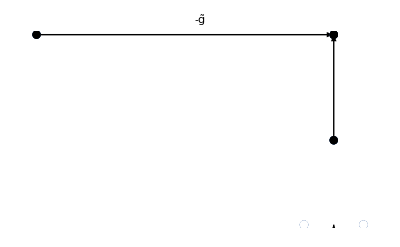

```mathematica
DrawFromContraction[-g̃ χs[Subscript[x, 2],1,2,Subscript[t, 1]] ψs[Subscript[x, 2],Subscript[t, 0]] Subscript[G, χ][Subscript[x, 2],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ψ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 1]]]
```

#### One-Loop

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, spaceIndex],timeIndex],{timeIndex,1,2}],{spaceIndex,0,1}];
```

```mathematica
OneLoop=WickContractionSpaceVerticesMOD[V[ϕs[Subscript[x, 0],Subscript[t, 1]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0/.V[_]->0;
```

```mathematica
OneLoopList=List @@ (OneLoop)/.Sum->List
%/.γ2->0
```

{ϕs[x_0,t_1],γ2 DD[ϕs[x_1,t_2] χs[x_1,1,2,t_1]] G_ϕ[x_1,x_0,t_1],-γ2 DD[χs[x_1,1,2,t_1]] ϕs[x_1,t_2] G_ϕ[x_1,x_0,t_1],-γ2^2 DD[ϕs[x_0,t_3] χs[x_0,1,2,t_2]] DD[χs[x_1,1,2,t_1]] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1],γ2^2 DD[χs[x_0,1,2,t_2]] DD[χs[x_1,1,2,t_1]] ϕs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1],-γ γ2 DD[χs[x_1,1,2,t_1]] g̃ ϕs[x_0,t_3] χs[x_0,1,2,t_2] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1],γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_2],γ γ2 DD[ϕs[x_0,t_3] χs[x_0,1,2,t_2]] g̃ χs[x_1,1,2,t_1] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_2],-γ γ2 DD[χs[x_0,1,2,t_2]] g̃ ϕs[x_0,t_3] χs[x_1,1,2,t_1] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_2],γ^2 (g̃)^2 ϕs[x_0,t_3] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3]^2 G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_2],γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2],γ γ2 DD[ϕs[x_0,t_3] χs[x_0,1,2,t_2]] g̃ χs[x_1,1,2,t_1] ψs[x_1,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2],-γ γ2 DD[χs[x_0,1,2,t_2]] g̃ ϕs[x_0,t_3] χs[x_1,1,2,t_1] ψs[x_1,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2],γ^2 (g̃)^2 ϕs[x_0,t_3] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2],-γ^2 (g̃)^3 ϕs[x_0,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_2]}

{ϕs[x_0,t_1],0,0,0,0,0,γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_2],0,0,γ^2 (g̃)^2 ϕs[x_0,t_3] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3]^2 G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_0,x_1,t_2],γ g̃ ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2],0,0,γ^2 (g̃)^2 ϕs[x_0,t_3] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] ψs[x_0,t_3] ψs[x_1,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,t_2],-γ^2 (g̃)^3 ϕs[x_0,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_0,t_3] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_0,t_2] G_ψ[x_1,x_1,t_2]}

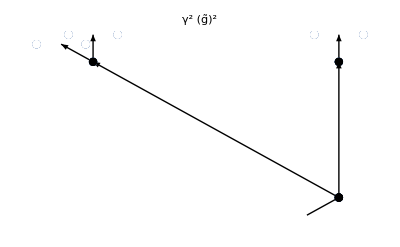

```mathematica
DrawFromContraction[OneLoopList[[-2]]/.γ2->0]
```

#### Two-Loop

I get some absurd result. Check that I can contract multiple g interactions at the same time

```mathematica
Z=Product[Product[InteractingAction[Subscript[x, spaceIndex],timeIndex],{timeIndex,1,3}],{spaceIndex,0,2}];
```

```mathematica
TwoLoop=WickContractionSpaceVerticesMOD[V[ϕs[Subscript[x, 0],Subscript[t, 1]]]*Z,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->4,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]/.Subscript[G, ϕ][a_,a_,b_] ->0/.Subscript[G, χ][a_,a_,b_] ->0/.V[_]->0;
```

```mathematica
TwoLoopList=List @@ (TwoLoop)/.Sum->List
```

{γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_2] χs[x_0,1,2,t_3] χs[x_2,1,2,t_1] ψs[x_2,t_4] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_1,t_3] G_χ[x_0,x_1,t_2] G_χ[x_0,x_2,t_3] G_ψ[x_0,x_1,t_3] G_ψ[x_0,x_2,t_2],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_2] χs[x_0,1,2,t_3] χs[x_1,1,2,t_1] ψs[x_1,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_2,t_3] G_ϕ[x_2,x_1,t_2] G_χ[x_0,x_1,t_3] G_χ[x_0,x_2,t_2] G_ψ[x_0,x_1,t_2] G_ψ[x_0,x_2,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_1,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_0,t_3] G_χ[x_0,x_1,t_3] G_χ[x_1,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_1,x_1,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_0,x_2,t_3] G_χ[x_1,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_1,x_1,t_2],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_1,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_2,t_3] G_ϕ[x_2,x_1,t_2] G_χ[x_0,x_1,t_3] G_χ[x_1,x_2,t_2] G_ψ[x_0,x_2,t_3] G_ψ[x_1,x_1,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_1,1,2,t_3] ψs[x_2,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_1,x_0,t_2] G_χ[x_1,x_2,t_3] G_ψ[x_1,x_0,t_3] G_ψ[x_1,x_1,t_2],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_0,1,2,t_2] χs[x_1,1,2,t_3] χs[x_2,1,2,t_1] ψs[x_0,t_4] G_ϕ[x_0,x_1,t_3] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_χ[x_0,x_1,t_2] G_χ[x_1,x_0,t_3] G_ψ[x_0,x_2,t_2] G_ψ[x_1,x_1,t_3],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_2] χs[x_1,1,2,t_3] χs[x_2,1,2,t_1] ψs[x_2,t_4] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_1,t_3] G_χ[x_0,x_1,t_2] G_χ[x_1,x_2,t_3] G_ψ[x_0,x_2,t_2] G_ψ[x_1,x_1,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_2] χs[x_2,1,2,t_1] ψs[x_1,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_1,x_0,t_3] G_ϕ[x_2,x_0,t_1] G_χ[x_0,x_1,t_3] G_χ[x_1,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_1,x_2,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_2] χs[x_2,1,2,t_1] ψs[x_2,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_0,x_2,t_3] G_χ[x_1,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_1,x_2,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_1,1,2,t_2] χs[x_1,1,2,t_3] χs[x_2,1,2,t_1] ψs[x_2,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_1,x_0,t_2] G_χ[x_1,x_2,t_3] G_ψ[x_1,x_0,t_3] G_ψ[x_1,x_2,t_2],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] χs[x_1,1,2,t_3] ψs[x_0,t_4] G_ϕ[x_0,x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_0,x_2,t_2] G_χ[x_1,x_0,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_1,x_2,t_3],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_1,1,2,t_3] ψs[x_0,t_4] G_ϕ[x_0,x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_0,t_3] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_2,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_1,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_0,t_3] G_χ[x_1,x_0,t_2] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_0,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_1,1,2,t_2] χs[x_2,1,2,t_1] χs[x_2,1,2,t_3] ψs[x_1,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_1,x_0,t_3] G_ϕ[x_2,x_0,t_1] G_χ[x_1,x_0,t_2] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_2,t_2] G_ψ[x_2,x_0,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_1,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_0,t_3] G_χ[x_0,x_1,t_3] G_χ[x_2,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_2,x_1,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_0,x_2,t_3] G_χ[x_2,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_2,x_1,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_1,1,2,t_1] χs[x_1,1,2,t_3] χs[x_2,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_0,t_2] G_ψ[x_1,x_0,t_3] G_ψ[x_2,x_1,t_2],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_1,t_4] G_ϕ[x_0,x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_0,t_3] G_χ[x_2,x_0,t_2] G_χ[x_2,x_1,t_3] G_ψ[x_2,x_0,t_3] G_ψ[x_2,x_1,t_2],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_0,1,2,t_2] χs[x_2,1,2,t_1] χs[x_2,1,2,t_3] ψs[x_0,t_4] G_ϕ[x_0,x_1,t_3] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_χ[x_0,x_1,t_2] G_χ[x_2,x_0,t_3] G_ψ[x_0,x_2,t_2] G_ψ[x_2,x_1,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_3] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_1,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_1,x_0,t_3] G_ϕ[x_2,x_0,t_1] G_χ[x_0,x_1,t_3] G_χ[x_2,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_3] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_0,x_2,t_3] G_χ[x_2,x_0,t_2] G_ψ[x_0,x_0,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_0,1,2,t_3] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_1,t_3] G_χ[x_0,x_2,t_3] G_χ[x_2,x_1,t_2] G_ψ[x_0,x_1,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_0,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_0,t_2] G_ψ[x_1,x_0,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_0,t_4] G_ϕ[x_0,x_1,t_3] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_χ[x_1,x_0,t_3] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_2,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_4] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_ϕ[x_2,x_1,t_3] G_χ[x_1,x_2,t_3] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_1,t_4] G_ϕ[x_0,x_2,t_2] G_ϕ[x_1,x_0,t_3] G_ϕ[x_2,x_0,t_1] G_χ[x_2,x_0,t_2] G_χ[x_2,x_1,t_3] G_ψ[x_2,x_0,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_2,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_0,t_4] G_ϕ[x_0,x_1,t_3] G_ϕ[x_1,x_2,t_2] G_ϕ[x_2,x_0,t_1] G_χ[x_2,x_0,t_3] G_χ[x_2,x_1,t_2] G_ψ[x_2,x_1,t_3] G_ψ[x_2,x_2,t_2],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] χs[x_2,1,2,t_3] ψs[x_0,t_4] G_ϕ[x_0,x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_0,x_2,t_2] G_χ[x_2,x_0,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_2,x_2,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_0,1,2,t_2] χs[x_1,1,2,t_1] χs[x_2,1,2,t_3] ψs[x_1,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_2,t_3] G_ϕ[x_2,x_1,t_2] G_χ[x_0,x_2,t_2] G_χ[x_2,x_1,t_3] G_ψ[x_0,x_1,t_2] G_ψ[x_2,x_2,t_3],γ^3 (g̃)^5 ϕs[x_0,t_4] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_0,t_4] G_ϕ[x_0,x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_χ[x_2,x_0,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3],γ^3 (g̃)^5 ϕs[x_1,t_4] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_1,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_1,x_2,t_3] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3]}

{γ^3,(g̃)^5,ϕs[x_2,t_4],ψs[x_0,t_4],G_ϕ[x_0,x_1,t_3],G_ϕ[x_1,x_2,t_2],G_ϕ[x_2,x_0,t_1],G_χ[x_0,x_1,t_2],G_χ[x_1,x_0,t_3],G_ψ[x_1,x_1,t_3],G_ψ[x_2,x_2,t_2]}

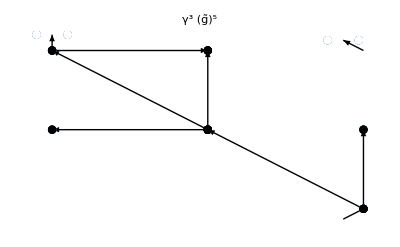

```mathematica
DrawFromContraction[TwoLoopList[[7]],"print"->True]
```

### Test without InteractingAction[]

```mathematica
WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

γ1 ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1]

#### 1-Loop

I  know I will have to use two γ_1 at 1-loop order. So, let’s set it up with two γ_1 at different times and space.

```mathematica
WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True]
```

γ^2 g_γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_3] ψs[x_action21,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_action21,x_1,t_2]

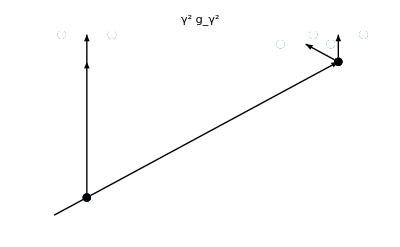

```mathematica
DrawFromContraction[%];
```

```mathematica
(* OK *)
```

Now, I would like to add the ψχ interaction vertex. However, I would like to let the program “decide freely” where and when to use it.

```mathematica
WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vψχ[Subscript[x, 101],t],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"killψ"->True,"maxContractions"->3]
```

-γ^2 g̃ g_γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_101,1,2,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_101,x_2,t_2] G_ψ[x_101,x_1,t_2]

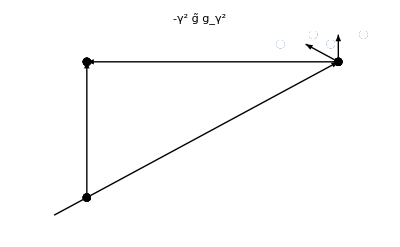

```mathematica
DrawFromContraction[%];
```

```mathematica
(* OK *)
```

#### 2-Loop

```mathematica
nInteractionVertices=2;AbsoluteTiming[TwoLoop1=WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Product[Vγ1[Subscript[x, ll],ll]Vψχ[Subscript[x, 100+ll],t],{ll,2,nInteractionVertices+1}],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(nInteractionVertices+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True];]
```

{0.773826,Null}

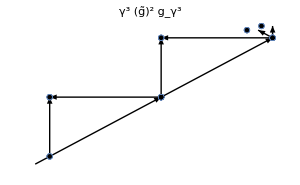
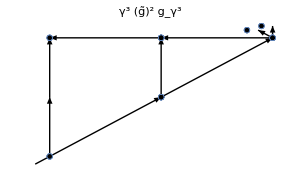
-Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[TwoLoop1,"print"->False,"showEndLines"->False,"ImageSize"->300];
```

```mathematica
(* OK!!! Finally working!! But wrong weights *)
```

#### 3-Loop

```mathematica
nInteractionVertices=3;
AbsoluteTiming[ThreeLoop3=WickContractionSpaceVerticesMOD[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Product[Vγ1[Subscript[x, ll],ll]Vψχ[Subscript[x, 100+ll],t],{ll,2,nInteractionVertices+1}],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->(nInteractionVertices+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True];]
```

{187.495,Null}

```mathematica
ThreeLoop3//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]]/.Subscript[G, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]Subscript[G, χ][Subscript[x, b_],Subscript[x, a_],Subscript[t, c_]]:>0
```

-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_2,1,2,t_3] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_3] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_3,t_3] G_χ[x_2,x_1,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_3] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_2,t_3] G_χ[x_2,x_3,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_3] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_4,t_4] G_χ[x_2,x_3,t_3] G_χ[x_3,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] χs[x_2,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_3,t_4] G_χ[x_2,x_3,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_3,1,2,t_3] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_2,t_2] G_χ[x_2,x_4,t_4] G_χ[x_3,x_2,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_2,t_2] G_χ[x_2,x_3,t_4] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_3] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_3,t_3] G_χ[x_2,x_4,t_4] G_χ[x_3,x_2,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_3] χs[x_2,1,2,t_2] χs[x_2,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_3,t_3] G_χ[x_2,x_3,t_4] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_4,t_4] G_χ[x_2,x_3,t_4] G_χ[x_3,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_χ[x_3,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_3,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_χ[x_3,x_2,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_3,t_4] G_χ[x_2,x_4,t_4] G_χ[x_3,x_2,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_3,t_4] G_χ[x_2,x_1,t_4] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_1,x_2,t_4] G_χ[x_2,x_3,t_4] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]

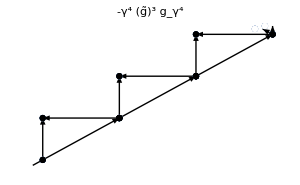
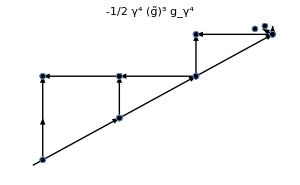
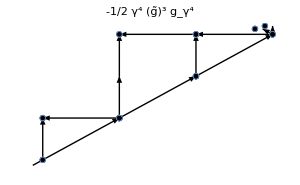
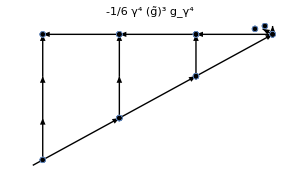
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[ThreeLoop3,"print"->False,"showEndLines"->False,"ImageSize"->300];
```

```mathematica
(* They are finally all there!!!!!! But they still have the wrong weight. Let's fix it*)
```

Manual list of diagrams (incomplete)

```mathematica
ThreeLoopList=List @@ (ThreeLoop)/.Sum->List
```

{-γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_102,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_2,t_2] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_1,t_2] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_3,t_4],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_3] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action2,t_3] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_102,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action2,t_3] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_3] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_2,t_3] G_ψ[x_103,x_action2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_102,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_2,t_3] G_ψ[x_103,x_action2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_3,1,2,t_3] χs[x_102,1,2,t_2] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_2,t_2] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_1,t_2] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action3,x_2,t_3],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_3,1,2,t_3] χs[x_102,1,2,t_2] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_2,t_2] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_1,t_2] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action3,x_2,t_3],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_3,1,2,t_3] χs[x_102,1,2,t_2] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_2,t_2] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_1,t_2] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action3,x_2,t_3],-1/2 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_3,1,2,t_3] χs[x_102,1,2,t_2] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_2,t_2] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_1,t_2] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action3,x_2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_4] χs[x_103,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action2,t_3] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action2,t_3] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action2,t_3] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action2,t_3] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_4] χs[x_103,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action2,t_3] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action2,t_3] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_4] χs[x_103,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_2,t_3] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_2,t_3] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_4] χs[x_103,1,2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_103,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_3,t_3] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_2,t_3] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_2,t_3] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/4 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_102,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_3,t_3] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_2,t_3] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_103,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_102,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_104,t_4] G_χ[x_103,x_4,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3],-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_102,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_4,t_4] G_χ[x_103,x_104,t_4] G_χ[x_104,x_103,t_4] G_ψ[x_102,x_3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_action3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3]}

{-1,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_2,t_2],G_χ[x_2,x_3,t_3],G_χ[x_3,x_4,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_2,x_2,t_3],G_ψ[x_3,x_3,t_4]}

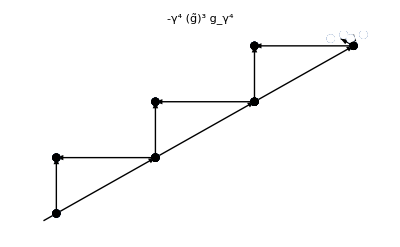

```mathematica
DrawFromContraction[ThreeLoopList[[1]],"print"->True,"showEndLines"->False];
```

{-1,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_2,t_3],G_χ[x_2,x_3,t_3],G_χ[x_3,x_4,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_2,x_2,t_3],G_ψ[x_3,x_3,t_4]}

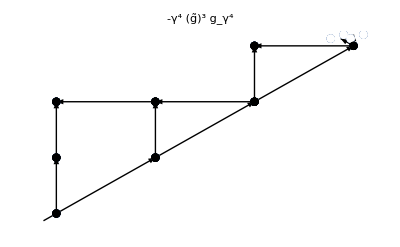

```mathematica
DrawFromContraction[ThreeLoopList[[2]]+ThreeLoopList[[5]],"print"->True,"showEndLines"->False];
```

```mathematica
DrawFromContraction[ThreeLoopList[[4]]+ThreeLoopList[[3]],"print"->True,"showEndLines"->False];
```

{-1,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_3,t_3],G_χ[x_2,x_1,t_3],G_χ[x_3,x_4,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_2,x_2,t_3],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[6]]+ThreeLoopList[[9]],"print"->True,"showEndLines"->False];
```

{-1,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_2,t_2],G_χ[x_2,x_3,t_4],G_χ[x_3,x_4,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_2,x_2,t_3],G_ψ[x_2,x_2,t_4],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[7]]+ThreeLoopList[[8]],"print"->True,"showEndLines"->False];
```

{-1,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_2,t_2],G_χ[x_2,x_4,t_4],G_χ[x_3,x_2,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_2,x_2,t_3],G_ψ[x_2,x_2,t_4],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[10]]+ThreeLoopList[[12]]+ThreeLoopList[[15]]+ThreeLoopList[[17]],"print"->True,"showEndLines"->False];
```

{-7/6,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_4],G_χ[x_3,x_4,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_2,x_2,t_3],G_ψ[x_2,x_2,t_4],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[11]]+ThreeLoopList[[13]]+ThreeLoopList[[14]]+ThreeLoopList[[16]],"print"->True,"showEndLines"->False];
```

{-7/6,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_3,t_3],G_χ[x_2,x_4,t_4],G_χ[x_3,x_2,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_2,x_2,t_3],G_ψ[x_2,x_2,t_4],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[18]]+ThreeLoopList[[20]]+ThreeLoopList[[23]]+ThreeLoopList[[25]],"print"->True,"showEndLines"->False];
```

{-7/6,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_3,t_4],G_χ[x_2,x_3,t_3],G_χ[x_3,x_4,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_1,x_1,t_4],G_ψ[x_2,x_2,t_3],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[19]]+ThreeLoopList[[21]]+ThreeLoopList[[22]]+ThreeLoopList[[24]],"print"->True,"showEndLines"->False];
```

{-7/6,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_1,x_4,t_4],G_χ[x_2,x_3,t_3],G_χ[x_3,x_1,t_4],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_1,x_1,t_4],G_ψ[x_2,x_2,t_3],G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
DrawFromContraction[ThreeLoopList[[26]],"print"->True,"showEndLines"->False];
```

{-1/3,γ^4,(g̃)^3,g_γ^4,ϕs[x_4,t_5],ψs[x_4,t_5],G_ϕ[x_1,x_0,t_1],G_ϕ[x_1,x_1,t_2],G_ϕ[x_3,x_1,t_3],G_ϕ[x_4,x_3,t_4],G_χ[x_3,x_4,t_4],G_χ[x_action3,x_action3,t_4]^2,G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3]^2,G_ψ[x_1,x_1,t_4]^2,G_ψ[x_3,x_3,t_4]}

-Graphics-

```mathematica
ThreeLoopList[[26]]
```

-1/3 γ^4 (g̃)^3 g_γ^4 ϕs[x_4,t_5] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_3,1,2,t_3] χs[x_104,1,2,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_χ[x_102,x_103,t_4] G_χ[x_103,x_102,t_4] G_χ[x_104,x_4,t_4] G_ψ[x_102,x_action3,t_4] G_ψ[x_103,x_action3,t_4] G_ψ[x_104,x_3,t_4] G_ψ[x_action2,x_1,t_2] G_ψ[x_action3,x_2,t_3] G_ψ[x_action3,x_action2,t_3]

## DrawFromContraction[]

The option to print multiple diagrams is already built-in

```mathematica
ClearAll[DrawFromContraction,x];
Options[DrawFromContraction]={"pointSize"->0.015,"print"->False,"showEndLines"->False,"ImageSize"->Medium};

(*DrawFromContraction[exp1_+exp2_,OptionsPattern[]]:=DrawFromContraction[exp1,"pointSize"->OptionValue["pointSize"],"print"->OptionValue["print"]]+DrawFromContraction[exp2,"pointSize"->OptionValue["pointSize"],"print"->OptionValue["print"]];*)

DrawFromContraction[exp_,OptionsPattern[]]:=Module[{terms,i,pureProp, weight, dots,plot},

terms=exp//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
//.DD[F_[A___,Subscript[x, a_],B___]]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>DD[F[A,Subscript[x, b],B]]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
//.DD[F_[A___,Subscript[x, a_],B___]H_[C___,Subscript[x, a_],D___]]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>DD[F[A,Subscript[x, b],B]H[C,Subscript[x, b],D]]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
//.DD[F_[A___,Subscript[x, d_],B___]H_[C___,Subscript[x, a_],D___]]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>DD[F[A,Subscript[x, d],B]H[C,Subscript[x, b],D]]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]]
/.Subscript[G, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]Subscript[G, χ][Subscript[x, b_],Subscript[x, a_],Subscript[t, c_]]:>0;

If[!OptionValue["showEndLines"], 
terms=terms/.χs[__]->1;
];

terms=List @@ (terms)/.Times->List;

If[OptionValue["print"],
Print[terms]];

(* I want to check if terms is a list of lists (which means that exp conatained a sum, i.e. multiple diagrams)*)
If[!Head[terms[[1]]] ===List,
(* TRUE: if it is not a List of lists *)

pureProp=DeleteElements[terms,{-1,g,g̃,Subscript[g, γ],γ,γ1,γ2,-g,-g̃,-Subscript[g, γ],-γ,-γ1,-γ2,g^(n_?NumericQ),(g̃)^(n_?NumericQ),Subscript[g, γ]^(n_?NumericQ),γ^(n_?NumericQ),γ1^(n_?NumericQ),γ2^(n_?NumericQ)}];
pureProp=DeleteCases[pureProp,_?NumericQ];

weight=Times@@DeleteElements[terms,pureProp];

pureProp=pureProp/.{DD[ϕs[Subscript[x, a_],Subscript[t, c_]] Subscript[F_, χ][Subscript[x, d_],Subscript[x, b_],Subscript[t, e_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, e]],Subscript[F, χ][Subscript[x, d],Subscript[x, b-0.1],Subscript[t, e]],ϕs[Subscript[x, a-0.1],Subscript[t, c]]},
DD[Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]χs[Subscript[x, d_],A___,Subscript[t, e_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, c-1]],Subscript[F, ϕ][Subscript[x, a],Subscript[x, b-0.1],Subscript[t, c]],χs[Subscript[x, d-0.1],A,Subscript[t, e]]},
DD[χs[Subscript[x, a_],A___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],χs[Subscript[x, a-0.1],A,Subscript[t, c]]},

DD[Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, c]],Subscript[F, χ][Subscript[x, a],Subscript[x, b-0.1],Subscript[t, c]]}};
pureProp=Flatten@pureProp;

(*Print[pureProp];*)

pureProp=pureProp//.{Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},n][[1]],FindArc[{b,c},{a,c},n][[2]],Darker[Green]],
(*Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]Subscript[F_, χ][Subscript[x, d_],Subscript[x, e_],Subscript[t, c_]]:>{Style[FindArc[{b,c},{a,c},1][[1]],FindArc[{b,c},{a,c},1][[2]],Darker[Green]],Style[FindArc[{e,c},{d,c},4][[1]],FindArc[{e,c},{d,c},4][[2]],Darker[Green]]},*)
(* THIS IS FOR TADPOLES*)
Subscript[F_, χ][Subscript[x, a_],Subscript[x, a_],Subscript[t, c_]]:>Style[FindArc[{a,c},{a+0.01,c},1][[1]],FindArc[{a,c},{a+0.01,c},1][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},(b-a)][[1]],FindArc[{b,c},{a,c},(b-a)][[2]],Darker[Green]],


Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},n][[1]],FindArc[{b,c-1},{a,c},n][[2]],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, 1]]:>Style[Line[{{a-0.13,1-0.13},{a,1}}],Arrowheads[{0,.03}],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},1][[1]],FindArc[{b,c-1},{a,c},1][[2]],Red],

Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},n][[1]],FindArc[{a,c-1},{a,c},n][[2]],Blue],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},1][[1]],FindArc[{a,c-1},{a,c},1][[2]],Blue],

Δ[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[Line[{{b,c},{a,c}}],Black,Dashed],

χs[Subscript[x, a_],__,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a+0.1,c}}],Arrowheads[{0,.03}],Darker[Green]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a-0.13,c-0.87}}],Arrowheads[{0,.03}],Red],
ψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a,c-0.8}}],Arrowheads[{0,.03}],Blue]};
pureProp=Flatten@pureProp;

	dots=Flatten[pureProp//.{
Style[Arrow[{{a_,c_},{b_,d_}}],___,color_]/;(IntegerQ[a*b*c*d]&&color=!=Blue):>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,d},Disk[{0,0},0.05],Black]},Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(!IntegerQ[a*b*c*d]):>{Style[{b+0.1,d},Disk[{0,0},0.05],White],Style[{b-0.1,d},Disk[{0,0},0.05],White]},
Style[Line[{{b_,c_},{a_,c_}}],Black,Dashed]:>{Style[{a,c},Disk[{0,0},0.05],Black]}
}];

plot=ListPlot[dots,
PlotLabel-> weight,
Axes->False,
Frame->False,
Mesh->Full,
AxesOrigin->{1,1}-0.2,
PlotStyle->PointSize[OptionValue["pointSize"]],
Prolog->pureProp,
ImagePadding->{{10,10},{10,10}},
PlotRangeClipping->False,
ImageSize->OptionValue["ImageSize"]];
Print[plot],

(* ELSE: if it is a list of lists *)
plot={};

For[i=1,i<=Length[terms],i++,

pureProp=DeleteElements[terms[[i]],{-1,g,g̃,Subscript[g, γ],γ,γ1,γ2,-g,-g̃,-Subscript[g, γ],-γ,-γ1,-γ2,g^(n_?NumericQ),(g̃)^(n_?NumericQ),Subscript[g, γ]^(n_?NumericQ),γ^(n_?NumericQ),γ1^(n_?NumericQ),γ2^(n_?NumericQ)}];
pureProp=DeleteCases[pureProp,_?NumericQ];

weight=Times@@DeleteElements[terms[[i]],pureProp];

pureProp=pureProp/.{DD[ϕs[Subscript[x, a_],Subscript[t, c_]] Subscript[F_, χ][Subscript[x, d_],Subscript[x, b_],Subscript[t, e_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, e]],Subscript[F, χ][Subscript[x, d],Subscript[x, b-0.1],Subscript[t, e]],ϕs[Subscript[x, a-0.1],Subscript[t, c]]},
DD[Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]χs[Subscript[x, d_],A___,Subscript[t, e_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, c-1]],Subscript[F, ϕ][Subscript[x, a],Subscript[x, b-0.1],Subscript[t, c]],χs[Subscript[x, d-0.1],A,Subscript[t, e]]},
DD[χs[Subscript[x, a_],A___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],χs[Subscript[x, a-0.1],A,Subscript[t, c]]},

DD[Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, c]],Subscript[F, χ][Subscript[x, a],Subscript[x, b-0.1],Subscript[t, c]]}};
pureProp=Flatten@pureProp;

(*Print[pureProp];*)

pureProp=pureProp/.{Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},n][[1]],FindArc[{b,c},{a,c},n][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, a_],Subscript[t, c_]]:>Style[FindArc[{a+0.5,c},{a,c},1][[1]],FindArc[{a+0.5,c},{a,c},1][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},(b-a)][[1]],FindArc[{b,c},{a,c},(b-a)][[2]],Darker[Green]],

Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},n][[1]],FindArc[{b,c-1},{a,c},n][[2]],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, c_]]:>Style[Line[{{a-0.13,c-0.13},{a,c}}],Arrowheads[{0,.03}],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},1][[1]],FindArc[{b,c-1},{a,c},1][[2]],Red],

Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},n][[1]],FindArc[{a,c-1},{a,c},n][[2]],Blue],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},1][[1]],FindArc[{a,c-1},{a,c},1][[2]],Blue],

Δ[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[Line[{{b,c},{a,c}}],Black,Dashed],

χs[Subscript[x, a_],__,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.1,c}}],Arrowheads[{0,.03}],Darker[Green]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a-0.13,c-0.87}}],Arrowheads[{0,.03}],Red],
ψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a,c-0.8}}],Arrowheads[{0,.03}],Blue]};

	dots=Flatten[pureProp//.{Style[Arrow[{{a_,c_},{b_,d_}}],___,color_]/;(IntegerQ[a*b*c*d]&&color=!=Blue):>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,d},Disk[{0,0},0.05],Black]},Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(!IntegerQ[a*b*c*d]):>{Style[{b-0.1,d},Disk[{0,0},0.05],White]},
Style[Line[{{b_,c_},{a_,c_}}],Black,Dashed]:>{Style[{a,c},Disk[{0,0},0.05],Black]}}];

AppendTo[plot,ListPlot[dots,
PlotLabel-> weight,
Axes->False,
Frame->False,
Mesh->Full,
AxesOrigin->{1,1}-0.2,
PlotStyle->PointSize[OptionValue["pointSize"]],
Prolog->pureProp,
ImagePadding->{{10,10},{10,10}},
PlotRangeClipping->False,
ImageSize->OptionValue["ImageSize"]]
];

];(*End of Loop*)
Print[Row[plot]];
](*End of IF*)
]
```

```mathematica
Print[Row[{1,2,3}," | "]]
```

|  | 123

#### Attempts

```mathematica
terms=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
terms=terms//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]]
```

-g γ1 γ2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_1,t_3] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]

```mathematica
terms=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
terms=terms//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]];
	terms=List @@ (terms);

	pureProp=Delete[terms,1];
	pureProp=DeleteElements[pureProp,{g,γ1,γ2,γ1g,γ2g}]

	weight=Times@@DeleteElements[terms,pureProp]

	pureProp=pureProp/.{Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},n][[1]],FindArc[{b,c},{a,c},n][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},1][[1]],FindArc[{b,c},{a,c},1][[2]],Darker[Green]],Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},n][[1]],FindArc[{b,c-1},{a,c},n][[2]],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},1][[1]],FindArc[{b,c-1},{a,c},1][[2]],Red],Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},n][[1]],FindArc[{a,c-1},{a,c},n][[2]],Blue],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},1][[1]],FindArc[{a,c-1},{a,c},1][[2]],Blue],
χs[Subscript[x, a_],__,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.1,c}}],Arrowheads[{0,.03}],Darker[Green]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a-0.13,c-0.87}}],Arrowheads[{0,.03}],Red],
ψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a,c-0.8}}],Arrowheads[{0,.03}],Blue]};

	dots=Flatten[pureProp//.{Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(IntegerQ[a*b*c*d]):>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,d},Disk[{0,0},0.05],Black]},Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(!IntegerQ[a*b*c*d]):>{Style[{0,d},Disk[{0,0},0.05],White]}}];
```

{ϕs[x_2,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_1,t_3],ψs[x_2,t_3],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_χ[x_1,x_2,t_2],G_ψ[x_1,x_1,t_2]}

-g γ1 γ2

```mathematica
IntegerQ[2*5*6*3.]
```

False

```mathematica
ListPlot[dots,
PlotLabel->ToString[ weight],
Axes->False,
Frame->False,
Mesh->Full,
(*AxesOrigin->dots[[1]]+0.01,*)
PlotStyle->PointSize[0.015],
Prolog->pureProp]
```

-Graphics-

```mathematica
dots={{1,1},{2,1},{2,2}};
styledDots={Style[{1,1},Disk[{0,0},0.1],Black],Style[{2,1},Disk[{0,0},0.1],White],Style[{2,2},Disk[{0,0},0.1],Black]};
ListPlot[styledDots,
Axes->False,
Frame->False,
Mesh->Full,
AxesOrigin->dots[[1]]+0.01,
PlotStyle->PointSize[0.03],
BaseStyle->Arrowheads[{0,.05,0}],
Prolog->{Style[Arrow[dots[[{1,2}]]],Red,Arrowheads[{0,-.05,0}]],
Style[FindArc[dots[[1]],dots[[3]],1][[1]],FindArc[dots[[1]],dots[[3]],1][[2]],Black],
Style[FindArc[dots[[1]],dots[[3]],2][[1]],FindArc[dots[[1]],dots[[3]],2][[2]],Red],
Style[FindArc[dots[[1]],dots[[3]],3][[1]],FindArc[dots[[1]],dots[[3]],3][[2]],Red]}]
```

-Graphics-

#### Tests

```mathematica
terms=-g γ γ ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
DrawFromContraction[terms]
```

-Graphics-

```mathematica
terms=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]]+g γ1 γ1 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
DrawFromContraction[terms]
```

{{g,γ1^2,ϕs[x_2,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_1,t_3],ψs[x_2,t_3],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_χ[x_1,x_2,t_2],G_ψ[x_1,x_1,t_2]},{-1,g,γ1,γ2,ϕs[x_2,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_1,t_3],ψs[x_2,t_3],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_χ[x_1,x_2,t_2],G_ψ[x_1,x_1,t_2]}}

-Graphics-

-Graphics-

## FindArc[]

```mathematica
Sign[-3]
```

-1

```mathematica
ClearAll[FindArc];

FindArc[dot1__,dot2__,order_]:=Module[{sub,px,py,qx,qy,cx,cy,r,radius,centerCoord,c,startAngle,endAngle,circle},

If[order==1 || order==-1,
Return[{Arrow[{dot1,dot2}],Arrowheads[{0,.05,0}]}]
];

sub={px:>dot1[[1]],py:>dot1[[2]],qx:>dot2[[1]],qy:>dot2[[2]]};

radius=EuclideanDistance[{px,py},{qx,qy}]/(1.07)^Abs[order]/.sub;

AppendTo[sub,r:>radius];

centerCoord=NSolve[{(px-cx)^2+(py-cy)^2==r^2,(qx-cx)^2+(qy-cy)^2==r^2}/.sub,{cx,cy}(*,Assumptions->r>0*)];
(*centerCoord=centerCoord/.sub;*)


c={cx,cy}/.centerCoord[[-Sign[order]]];


startAngle=ArcTan[px-c[[1]],py-c[[2]]]/.sub;

endAngle=ArcTan[qx-c[[1]],qy-c[[2]]]/.sub;

circle=Circle[c,radius,{startAngle,endAngle}];

Return[{Arrow[circle],Arrowheads[{0,(.05),0}]}];
]
```

#### Test

```mathematica
Solve[{(1-cx)^2+(2-cy)^2==r^2,(3-cx)^2+(2-cy)^2==r^2},{cx,cy},Assumptions->r>0]
%/.r->1.7468774565464231
```

{{cx→2,cy→2-√(-1+r^2)},{cx→2,cy→2+√(-1+r^2)}}

{{cx→2,cy→0.567666},{cx→2,cy→3.43233}}

```mathematica
FindArc[{1,2},{3,2},2]
```

{Arrow[Circle[{2.,3.43233},1.74688,{-2.18029,-0.961306}]],Arrowheads[{0,0.05,0}]}

```mathematica
ToExpression[StringReplace[ToString[FindArc[dots[[1]],dots[[3]],2]],{"{"->"","}"->"",", "->","}]]
```

ToExpression::sntx: Invalid syntax in or before "Arrow[Circle[0.783833,2.21617,1.23523,-1.39489,-0.175907]],Arrowheads[0,0.05,0]".
                                                                                                            ^

$Failed

```mathematica
Graphics[{Arrow[Circle[{0,0},1,{π,π/2}]]}]
```

-Graphics-

```mathematica
Graphics[{Arrow[FindArc[dots[[1]],dots[[3]],1]],Red,Point[dots[[{1,3}]]]}]
Graphics[{Arrow[FindArc[dots[[1]],dots[[3]],2]],Red,Point[dots[[{1,3}]]]}]
Graphics[{Arrow[FindArc[dots[[1]],dots[[3]],3]],Red,Point[dots[[{1,3}]]]}]
```

Part::partd: Part specification dots⟦1⟧ is longer than depth of object.

Part::partd: Part specification dots⟦3⟧ is longer than depth of object.

Part::partd: Part specification dots⟦{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification dots⟦1⟧ is longer than depth of object.

Part::partd: Part specification dots⟦3⟧ is longer than depth of object.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partd: Part specification dots⟦{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification dots⟦1⟧ is longer than depth of object.

Part::partd: Part specification dots⟦3⟧ is longer than depth of object.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partd: Part specification dots⟦{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
sub={px->dots[[1,1]],py->dots[[1,2]],qx->dots[[3,1]],qy->dots[[3,2]]};
rad=EuclideanDistance[{px,py},{qx,qy}]/(1.07)^3/.sub;
AppendTo[sub,r->rad];
centerCoord=Solve[{(px-cx)^2+(py-cy)^2==r^2,(qx-cx)^2+(qy-cy)^2==r^2},{cx,cy},Assumptions->r>0];
centerCoord/.sub;
c={cx,cy}/.%[[2]];
startAngle=(ArcTan[px-c[[1]],py-c[[2]]])/.sub;
endAngle=(ArcTan[qx-c[[1]],qy-c[[2]]])/.sub;

Graphics[{Circle[c,rad,{startAngle,endAngle}],Red,Point[dots[[{1,3}]]]}]
```

-Graphics-

## ToMomentumSpace

```mathematica
ClearAll[ToMomentumSpace];
Options[ToMomentumSpace]={"print"->False,"mχ"->m2χ,"mϕ"->m2ϕ,"amputateLegs"->{χs},"origins"->False};

ToMomentumSpace[exp_,OptionsPattern[]]:=Module[{terms,pureProp,externalLegs,weight,momentumExp,i,j,m2χ,m2ϕ,ptot},
ptot=0;
m2χ=OptionValue["mχ"];
m2ϕ=OptionValue["mϕ"];

If[OptionValue["print"],
Print[Style["\t Mass values: ",{Blue}],"mχ = ",OptionValue["mχ"],", mϕ = ",OptionValue["mϕ"] ]
];


terms=exp//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
//.DD[F_[A___,Subscript[x, a_],B___]]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>DD[F[A,Subscript[x, b],B]]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
//.DD[F_[A___,Subscript[x, a_],B___]H_[C___,Subscript[x, a_],D___]]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>DD[F[A,Subscript[x, b],B]H[C,Subscript[x, b],D]]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
//.DD[F_[A___,Subscript[x, d_],B___]H_[C___,Subscript[x, a_],D___]]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>DD[F[A,Subscript[x, d],B]H[C,Subscript[x, b],D]]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]
/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]];
terms=List @@ (terms);

pureProp=DeleteElements[terms,{g,γ1,γ2,γ1g,γ2g,g^_,γ1^_,γ2^_,γ1g^_,γ2g^_}];

externalLegs= DeleteElements[pureProp,{Subscript[G, _][___],DD[Subscript[G, _][___]],DD[F_[___]Subscript[G, _][___]]}];

weight=Times@@DeleteElements[terms,pureProp];

For[i=1, i<=Length[pureProp],i++,
pureProp[[i]]=pureProp[[i]]/.{Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>(1/(γ(s[Subscript[p, i]]+m2ϕ)))^n δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, c_]]:>ϕ[k]δ[k,Subscript[x, a],Subscript[t, c]],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>1/(γ(s[Subscript[p, i]]+m2ϕ))δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],

Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>(1/(s[Subscript[p, i]]+m2χ))^n δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>1/(s[Subscript[p, i]]+m2χ)δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c]],

Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],

χs[Subscript[x, a_],___,Subscript[t, c_]]:>χs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>ϕs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c-1]],
ψs[Subscript[x, a_],Subscript[t, c_]]:>ψs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c-1]],

DD[ϕs[Subscript[x, a_],Subscript[t, c_]] Subscript[F_, χ][Subscript[x, d_],Subscript[x, b_],Subscript[t, e_]]]:>-s[Subscript[p, i]+Subscript[q, i]]ϕs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c-1]] 1/(s[Subscript[q, i]]+m2χ)δ[Subscript[q, i],Subscript[x, d],Subscript[t, e]]δ[-Subscript[q, i],Subscript[x, b],Subscript[t, e]],
DD[Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]χs[Subscript[x, d_],___,Subscript[t, e_]]]:>-s[Subscript[p, i]+Subscript[q, i]]χs[Subscript[q, i]]δ[Subscript[q, i],Subscript[x, d],Subscript[t, e]] 1/(γ(s[Subscript[p, i]]+m2ϕ))δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],
DD[χs[Subscript[x, a_],___,Subscript[t, c_]]]:>-s[Subscript[p, i]]χs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]],

DD[Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>-s[Subscript[p, i]] 1/(s[Subscript[p, i]]+m2χ)δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c]]};
ptot+=Subscript[p, i];
];


momentumExp = Times@@pureProp;


For[i=1, i<=Length[pureProp],i++,
(*If[OptionValue["origins"],
If[!FreeQ[momentumExp,χs[Subscript[p, i]]],
Print[]
]
];*)
If[!FreeQ[momentumExp,Subscript[q, i]],
ptot+=Subscript[q, i]];
];

(*momentumExp=momentumExp*WannaBeDiracDelta[ptot+k];*)

If[OptionValue["print"],
Print[Style["\n\t Expression in momentum space, not yet integrated:\n",{Blue}],momentumExp ]
];


(* VERTEX MOMENTUM CONSERVATION *)

momentumExp=momentumExp//.δ[ Subscript[p, b_],A___]δ[a_,A___]:>δ[a+ Subscript[p, b],A]//.δ[- Subscript[p, b_],A___]δ[a_,A___]:>δ[a- Subscript[p, b],A];
momentumExp=momentumExp//.δ[a_,A___]δ[ Subscript[q, b_],A___]:>δ[a+ Subscript[q, b],A]//.δ[a_,A___]δ[- Subscript[q, b_],A___]:>δ[a- Subscript[q, b],A]/.δ[a_+Subscript[p, b_],A___]:>DiracDelta[a+ Subscript[p, b]]ⅆ Subscript[p, b];

If[OptionValue["print"],
Print[Style["\n\t Setting up momentum conservation\n",{Blue}],momentumExp ]
];

While[!FreeQ[momentumExp,ⅆ Subscript[p, a_]],
For[i=1, i<=Length[pureProp],i++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, i]],
If[FreeQ[momentumExp,DiracDelta[Subscript[p, i]+A__]DiracDelta[Subscript[p, i]+B__]] && FreeQ[momentumExp,DiracDelta[-Subscript[p, i]+A__]DiracDelta[Subscript[p, i]+B__]] &&FreeQ[momentumExp,DiracDelta[-Subscript[p, i]+A__]DiracDelta[-Subscript[p, i]+B__]]  ,
momentumExp=Integrate[momentumExp /.ⅆ Subscript[p, i]->1,{Subscript[p, i],-∞,∞},GenerateConditions->False],
(*ELSE*)
Continue[];
]
]
]
];


If[OptionValue["print"],
Print[Style["\n\t Implementing momentum conservation at vertices\n",{Blue}],momentumExp ]
];
(*
(* TOTAL MOMENTUM CONSERVATION *)
momentumExp=momentumExp/.WannaBeDiracDelta[a_+Subscript[p, b_]]:>DiracDelta[a+Subscript[p, b]]ⅆ Subscript[p, b];

If[OptionValue["print"],
Print[Style["\n\t Setting up TOTAL momentum conservation\n",{Blue}],momentumExp ]
];

For[i=1, i<=Length[pureProp],i++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, i]],
momentumExp=Integrate[momentumExp /.ⅆ Subscript[p, i]->1,{Subscript[p, i],-∞,∞},GenerateConditions->False];
]
];

If[OptionValue["print"],
Print[Style["\n\t Implementing TOTAL momentum conservation\n",{Blue}],momentumExp ]
];
*)

(* MOMENTA REORDERING *)

j=Length[pureProp];

For[i=1, i<=Length[externalLegs],i++,
If[FreeQ[momentumExp,Subscript[p, i]],
momentumExp=momentumExp/.Subscript[q, i]->Subscript[p, i];
];
];

For[i=1, i<=Length[externalLegs],i++,
While[FreeQ[momentumExp,Subscript[p, i]],
momentumExp=momentumExp/.Subscript[p, j]->Subscript[p, i];
j--;
];
];

If[OptionValue["print"],
Print[Style["\n\t Reordering momenta\n",{Blue}],momentumExp ]
];

(* LEG AMPUTATION *)
If[Length[OptionValue["amputateLegs"]]=!=0,
For[i=1, i<=Length[OptionValue["amputateLegs"]],i++,

momentumExp=momentumExp/.{OptionValue["amputateLegs"][[i]][a_+Subscript[p, b_]]:>OptionValue["amputateLegs"][[i]][a+Subscript[p, b]]WannaBeDiracDelta[a+Subscript[p, b]]ⅆ Subscript[p, b],OptionValue["amputateLegs"][[i]][a_-Subscript[p, b_]]:>OptionValue["amputateLegs"][[i]][a-Subscript[p, b]]WannaBeDiracDelta[a-Subscript[p, b]]ⅆ Subscript[p, b]}
/.OptionValue["amputateLegs"][[i]][Subscript[p, b_]]:>OptionValue["amputateLegs"][[i]][Subscript[p, b]]WannaBeDiracDelta[Subscript[p, b]]ⅆ Subscript[p, b];



(*
momentumExp=momentumExp//.WannaBeDiracDelta[a_]WannaBeDiracDelta[c_+Subscript[p, b_]]/;(!FreeQ[a,Subscript[p, b]]):>WannaBeDiracDelta[a-Subscript[p, b]-c]//.WannaBeDiracDelta[a_]WannaBeDiracDelta[c_-Subscript[p, b_]]/;(!FreeQ[a,Subscript[p, b]]):>WannaBeDiracDelta[a-Subscript[p, b]+c]/.WannaBeDiracDelta[a_+Subscript[p, b_]]:>DiracDelta[a+Subscript[p, b]]ⅆ Subscript[p, b]/.WannaBeDiracDelta[a_-Subscript[p, b_]]:>DiracDelta[a-Subscript[p, b]]ⅆ Subscript[p, b];


Print["\n",momentumExp,"\n"];
*)

momentumExp=momentumExp/.WannaBeDiracDelta[a_+c_ Subscript[p, b_]+d_ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[a+ c Subscript[p, b]+d Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[c_ Subscript[p, b_]+d_ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[c Subscript[p, b]+d Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[a_+ Subscript[p, b_]+d_ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[a+ Subscript[p, b]+ d Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[ Subscript[p, b_]+d_ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[ Subscript[p, b]+d Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[a_+ d_ Subscript[p, b_]+ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[a+ d Subscript[p, b]+  Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[ d_ Subscript[p, b_]+ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[d Subscript[p, b]+ Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[a_+ Subscript[p, b_]+ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[a+  Subscript[p, b]+  Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]
/.WannaBeDiracDelta[  Subscript[p, b_]+ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[ Subscript[p, b]+ Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b];


If[OptionValue["print"],
Print[Style["\n\t Setting up the amputation ofthe fields ",{Blue}],Style[OptionValue["amputateLegs"][[i]],{Blue}],"\n",momentumExp,"\n"];
];

For[j=1, j<=Length[pureProp],j++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, j]],

momentumExp=momentumExp /.{WannaBeDiracDelta[a_]/;(!FreeQ[a,Subscript[p, j]] ):>DiracDelta[a],ⅆ Subscript[p, j]->1}//.DiracDelta[a_]DiracDelta[b_]/;(!FreeQ[a,Subscript[p, j]] && !FreeQ[b,Subscript[p, j]]):>WannaBeDiracDelta[a]DiracDelta[b];
momentumExp=Integrate[momentumExp,{Subscript[p, j],-∞,∞},GenerateConditions->False];
]
];

If[OptionValue["print"],
Print[Style["\n\t Amputating the fields ",{Blue}],Style[OptionValue["amputateLegs"][[i]],{Blue}],Style[" \n",{Blue}],momentumExp ]
];
];
];


If[OptionValue["print"],Print["\n"]];

Return[momentumExp];
]
```

#### Attempts

```mathematica
momentumExp=(Subscript[p, 1]+Subscript[p, 2])DiracDelta[Subscript[p, 1]+Subscript[p, 2]+Subscript[p, 3]]ⅆ Subscript[p, 1];
For[i=1, i<=3,i++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, i]],
momentumExp=Integrate[momentumExp /.ⅆ Subscript[p, i]->1,{Subscript[p, i],-∞,∞},GenerateConditions->False];
]
];
momentumExp
```

-p_3

```mathematica
ptot=Subscript[p, 1]+Subscript[p, 2];
momentumExp=ptot DiracDelta[Subscript[p, 1]+Subscript[p, 2]+Subscript[p, 3]]ⅆptot;
Integrate[momentumExp /.ⅆptot->1,{ptot,-∞,∞},GenerateConditions->False]
```

Integrate::ilim: Invalid integration variable or limit(s) in {p_1+p_2,-∞,∞}.

Integrate[DiracDelta[p_1+p_2+p_3] (p_1+p_2),{p_1+p_2,-∞,∞},GenerateConditions→False]

#### Test

g γ1 γ1

```mathematica
expgγ1γ1=-g γ1 γ1 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
```

```mathematica
DrawFromContraction[expgγ1γ1]
```

-Graphics-

```mathematica
exp=expgγ1γ1;
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ψs}]
```

(ϕ[k] ϕs[-k] χs[0]^2 ψs[0]^2)/(γ (m2ϕ+s[p_3]) (m2χ+s[-k+p_3]))

```mathematica
(* ok it seems to be working *)
```

g γ1 γ2

```mathematica
expgγ1γ2=WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ2[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 γ2 DD[ϕs[x_2,t_3] G_χ[x_3,x_2,t_2]] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_2,t_3] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
DrawFromContraction[expgγ1γ2]
```

{Δ[x_1.9,x_2,t_2],G_χ[x_1,x_1.9,t_2],ϕs[x_1.9,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_1,t_3],ψs[x_2,t_3],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ψ[x_1,x_1,t_2]}

-Graphics-

```mathematica
exp=expgγ1γ2;
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
expgγ1γ2Mom=%/.Subscript[p, 5]->0
```

(s[-k+p_3-p_5] ϕ[k] ϕs[0] χs[0]^2 ψs[-k-p_5] ψs[p_5])/(γ (m2ϕ+s[p_3]) (m2χ+s[-k+p_3-p_5]))

(s[-k+p_3] ϕ[k] ϕs[0] χs[0]^2 ψs[0] ψs[-k])/(γ (m2ϕ+s[p_3]) (m2χ+s[-k+p_3]))

g γ1 γ2Minus

```mathematica
expgγ1γ2Minus=WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ2Minus[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

g γ1 γ2 DD[G_χ[x_3,x_2,t_2]] ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
DrawFromContraction[expgγ1γ2Minus]
```

-Graphics-

```mathematica
exp=expgγ1γ2Minus;
expgγ1γ2MinusMom=ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
```

{g,γ1,γ2,DD[G_χ[x_1,x_2,t_2]],ϕs[x_2,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_1,t_3],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ψ[x_1,x_1,t_2]}

-(s[p_2] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p_2]) (m2χ+s[p_2]))

Their sum

```mathematica
expgγ1γ2Mom+expgγ1γ2MinusMom/.m2χ->0/.Subscript[p, 2]->Subscript[p, 3]//FullSimplify
```

(ϕ[k] ϕs[0] χs[0]^2 (-1+ψs[0]) ψs[-k])/(γ (m2ϕ+s[p_3]))

```mathematica
(* LOOKS OK *)
```

# DIAGRAMS FOR ψ-PLUCKING OBSERVABLE

## Order g

### gγ_1^2

```mathematica
expgγ1γ1=WickContractionSpaceVertices[Vγ1[Subscript[x, 2],2]Vγ1[Subscript[x, 1],1]Vψχ[Subscript[x, 3],2] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

-g γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_2,t_3] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_3,x_2,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
DrawFromContraction[expgγ1γ1]
```

-Graphics-

```mathematica
exp=expgγ1γ1;
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]

DIAGgγ1γ1Pluckψ=%/.{Subscript[p, 3]->p,Subscript[p, 6]->0}
```

-(ϕ[k] ϕs[0] χs[0]^2 ψs[-k-p_6] ψs[p_6])/(γ (m2ϕ+s[p_3]) (m2χ+s[-k+p_3-p_6]))

-(ϕ[k] ϕs[0] χs[0]^2 ψs[0] ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[-k+p]))

```mathematica
(* THIS IS THE BANANA *)
```

### gγ_1 γ_2

```mathematica
expgγ1γ2=WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]Vγ2[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

-g γ1 γ2 DD[ϕs[x_2,t_3] G_χ[x_3,x_2,t_2]] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
DrawFromContraction[expgγ1γ2]
```

-Graphics-

```mathematica
exp=expgγ1γ2;
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
DIAGgγ1γ2Pluckψ=%/.{Subscript[p, 3]->p}
```

(s[p_3] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p_3]) (m2χ+s[p_3]))

(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

### gγ_1 γ_2minus

```mathematica
expgγ1γ2minus=WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]Vγ2Minus[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

g γ1 γ2 DD[G_χ[x_3,x_2,t_2]] ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
DrawFromContraction[expgγ1γ2minus]
```

-Graphics-

```mathematica
exp=expgγ1γ2minus;
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
DIAGgγ1γ2minusPluckψ=%/.{Subscript[p, 2]->p}
```

-(s[p_2] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p_2]) (m2χ+s[p_2]))

-(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

#### gγ_1 γ_2+gγ_1 γ_2minus

```mathematica
DIAGgγ1γ2Pluckψ
DIAGgγ1γ2minusPluckψ
%%+%
```

(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

-(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

0

```mathematica
(* IF I AM INTERESTED IN PLUCKING PSI, THEN I GET EXACT CANCELLATION INDEPENDENTLY OF THE MASSES (expected because no momentum in the outgoing red line)*)
```

## Order g^2

### g^2 γ_1^3.A

I have to be careful and use the g-vertices in the right positions

```mathematica
expg2γ1γ1γ1A=WickContractionSpaceVerticesMOD[Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vγ1[Subscript[x, 3],3]Vψχ[Subscript[x, 4],2]Vψχ[Subscript[x, 5],3] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_4,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_3,t_4] ψs[x_5,t_4] ψs[x_action3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_2,t_2] G_χ[x_5,x_3,t_3] G_ψ[x_4,x_1,t_2] G_ψ[x_5,x_2,t_3] G_ψ[x_action3,x_4,t_3]

```mathematica
DrawFromContraction[expg2γ1γ1γ1A]
```

-Graphics-

```mathematica
exp=expg2γ1γ1γ1A;
tempDiag=ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
```

(ϕ[k] ϕs[0] χs[0]^3 ψs[p_6] ψs[-k-p_6-p_7] ψs[p_7])/(γ^2 (m2χ+s[p_5]) (m2ϕ+s[p_5-p_6-p_7]) (m2ϕ+s[p_10]) (m2χ+s[p_7+p_10]))

```mathematica
DIAGg2γ1γ1γ1APluckψ=tempDiag/.{Subscript[p, 5]->p,Subscript[p, 10]->q,Subscript[p, 6]->0,Subscript[p, 7]->-k}
```

(ϕ[k] ϕs[0] χs[0]^3 ψs[0]^2 ψs[-k])/(γ^2 (m2χ+s[p]) (m2ϕ+s[k+p]) (m2ϕ+s[q]) (m2χ+s[-k+q]))

```mathematica
(* THIS IS THE DOUBLE BANANA *)
```

### g^2 γ_1^3.B

I have to be careful and use the g-vertices in the right positions

```mathematica
expg2γ1γ1γ1B=WickContractionSpaceVerticesMOD[Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vγ1[Subscript[x, 3],3]Vψχ[Subscript[x, 4],3]Vψχ[Subscript[x, 5],3] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"maxContractions"->6,"killψ"->True]
```

g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_3,t_4] ψs[x_4,t_4] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_3,t_3] G_χ[x_5,x_4,t_3] G_ψ[x_4,x_2,t_3] G_ψ[x_5,x_action2,t_3] G_ψ[x_action2,x_1,t_2]+g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_4,1,2,t_3] ψs[x_3,t_4] ψs[x_4,t_4] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_3,t_3] G_χ[x_5,x_5,t_3] G_ψ[x_4,x_2,t_3] G_ψ[x_5,x_action2,t_3] G_ψ[x_action2,x_1,t_2]

```mathematica
list=List@@expg2γ1γ1γ1B
```

{g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_3,t_4] ψs[x_4,t_4] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_3,t_3] G_χ[x_5,x_4,t_3] G_ψ[x_4,x_2,t_3] G_ψ[x_5,x_action2,t_3] G_ψ[x_action2,x_1,t_2],g^2 γ1^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] χs[x_4,1,2,t_3] ψs[x_3,t_4] ψs[x_4,t_4] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_4,x_3,t_3] G_χ[x_5,x_5,t_3] G_ψ[x_4,x_2,t_3] G_ψ[x_5,x_action2,t_3] G_ψ[x_action2,x_1,t_2]}

```mathematica
DrawFromContraction[list[[1]]]
```

-Graphics-

```mathematica
DrawFromContraction[list[[2]],"print"->True]
```

{g^2,γ1^3,ϕs[x_3,t_4],χs[x_1,1,2,t_1],χs[x_2,1,2,t_2],χs[x_2,1,2,t_3],ψs[x_1,t_4],ψs[x_2,t_4],ψs[x_3,t_4],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_ϕ[x_3,x_2,t_3],G_χ[x_1,x_1,t_3],G_χ[x_2,x_3,t_3],G_ψ[x_1,x_1,t_2],G_ψ[x_1,x_1,t_3],G_ψ[x_2,x_2,t_3]}

-Graphics-

## WORKING HERE: missing hat

```mathematica
(* OF THESE TWO DIAGRAMS, THE SECOND ONE HAS A TADPOLE, NOT PROPERLY DISPLAYED. HOWEVER, I AM STILL MISSING THE HAT...*)
```

```mathematica
exp=list[[1]];
tempDiag=ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
```

(ϕ[k] ϕs[0] χs[0]^3 ψs[p_5] ψs[-k-p_5-p_7] ψs[p_7])/(γ^2 (m2ϕ+s[p_6]) (m2χ+s[p_6+p_7]) (m2ϕ+s[p_9]) (m2χ+s[-k-p_5+p_9]))

```mathematica
DIAGg2γ1γ1γ1BPluckψ=tempDiag/.{Subscript[p, 6]->p,Subscript[p, 9]->q,Subscript[p, 5]->0,Subscript[p, 7]->-k}
```

(ϕ[k] ϕs[0] χs[0]^3 ψs[0]^2 ψs[-k])/(γ^2 (m2ϕ+s[p]) (m2χ+s[-k+p]) (m2ϕ+s[q]) (m2χ+s[-k+q]))

```mathematica
(* THIS IS A SECOND DOUBLE BANANA *)
```

Attempts to get the hat

```mathematica
WickContractionSpaceVerticesMOD[Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 3],2]Vγ1[Subscript[x, 2],3]Vψχ[Subscript[x, 5],3]Vψχ[Subscript[x, 4],3] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ψ,ϕ,χ}], "endTime"->3,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1,"maxContractions"->6,"killψ"->True];
list=List@@%;
list[[1]]
DrawFromContraction[list[[1]]]
```

g^2 γ1^3 ϕs[x_2,t_4] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] χs[x_5,1,2,t_3] ψs[x_2,t_4] ψs[x_4,t_4] ψs[x_5,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_3,t_3] G_ϕ[x_3,x_1,t_2] G_χ[x_4,x_2,t_3] G_χ[x_5,x_4,t_3] G_ψ[x_4,x_3,t_3] G_ψ[x_5,x_action2,t_3] G_ψ[x_action2,x_1,t_2]

-Graphics-

```mathematica
Subscript[G, χ][Subscript[x, 4],Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 5],Subscript[x, 4],Subscript[t, 3]]/.{Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]Subscript[F_, χ][Subscript[x, d_],Subscript[x, e_],Subscript[t, c_]]:>{Style[FindArc[{b,c},{a,c},2][[1]],FindArc[{b,c},{a,c},2][[2]],Darker[Green]],Style[FindArc[{e,c},{d,c},1][[1]],FindArc[{e,c},{d,c},1][[2]],Darker[Green]]}}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Arrow[Circle[{3.,Indeterminate},1.74688,{Indeterminate,Indeterminate}]],Arrow[{{4,3},{5,3}}]}

```mathematica
FindArc[{1,1},{1,1},2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Arrow[Circle[{Indeterminate,Indeterminate},0.,{Indeterminate,Indeterminate}]],Arrowheads[{0,0.05,0}]}

### gγ_1 γ_2minus

```mathematica
expgγ1γ2minus=WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]Vγ2Minus[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2] ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

g γ1 γ2 DD[G_χ[x_3,x_2,t_2]] ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
DrawFromContraction[expgγ1γ2minus]
```

-Graphics-

```mathematica
exp=expgγ1γ2minus;
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ϕs}]
DIAGgγ1γ2minusPluckψ=%/.{Subscript[p, 2]->p}
```

-(s[p_2] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p_2]) (m2χ+s[p_2]))

-(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

#### gγ_1 γ_2+gγ_1 γ_2minus

```mathematica
DIAGgγ1γ2Pluckψ
DIAGgγ1γ2minusPluckψ
%%+%
```

(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

-(s[p] ϕ[k] ϕs[0] χs[0]^2 ψs[-k])/(γ (m2ϕ+s[p]) (m2χ+s[p]))

0

```mathematica
(* IF I AM INTERESTED IN PLUCKING PSI, THEN I GET EXACT CANCELLATION INDEPENDENTLY OF THE MASSES (expected because no momentum in the outgoing red line)*)
```

ResourceSubmit::rscloudc: You must connect to the Wolfram cloud to submit the resource. Please use CloudConnect to establish a connection with the Wolfram cloud.